```mathematica
Needs["WSMLink`"]
tauList={};
tau=4;
fP=0.01;
g=0;
thetaList={};
theta=1.1;
vectorList={};
phiTrials=1;
notFPTracker=True;
desiredLimit=1;
trialLimit=10000;
fPList={};
components={"F_A"∈"Modelica.Blocks.Sources.Ramp", "F_P"∈"Modelica.Blocks.Sources.Constant", "RJT"∈"Modelica.Blocks.Sources.Ramp","LT"∈"Modelica.Blocks.Sources.Constant", "BMJEC"∈"PowerGrab.Components.BoneMuscleJointExperimentalComponent", "world"∈"Modelica.Mechanics.MultiBody.World"};
connections={"F_A.y"->"BMJEC.F_A","F_P.y"->"BMJEC.F_P","LT.y"->"BMJEC.LoadTorque", "RJT.y"->"BMJEC.RevoluteJointTheta", "world.frame_b"->"BMJEC.frame_a"};
mmodel=WSMConnectComponents["JTest",components,connections];
tauComponents={"F_A"∈"Modelica.Blocks.Sources.Ramp", "F_P"∈"Modelica.Blocks.Sources.Constant", "RJT"∈"Modelica.Blocks.Sources.Ramp","LT"∈"Modelica.Blocks.Sources.Constant", "BMJEC"∈"PowerGrab.Components.BoneMuscleJointExperimentalComponent", "world"∈"Modelica.Mechanics.MultiBody.World"};
tauConnections={"F_A.y"->"BMJEC.F_A","F_P.y"->"BMJEC.F_P","LT.y"->"BMJEC.LoadTorque", "RJT.y"->"BMJEC.RevoluteJointTheta", "world.frame_b"->"BMJEC.frame_a"};
taumodel=WSMConnectComponents["TauTest",components,connections];
While[phiTrials≤trialLimit,
Print["tau = ", tau, ", theta = ", theta, ", Trial number = ", phiTrials, ", fP = ", fP];
AppendTo[fPList,fP];
WSMSetValues[mmodel,{"F_A.duration"->10,"F_P.k"->fP,"LT.k"->tau,"RJT.duration"->0,"RJT.height"->0,"RJT.offset"->theta,"world.g"-> g,"BMJEC.phi_0_restrained"->theta}];
MM=WSMSimulate[mmodel,{0,10}];
tauFunction=First[MM[{"BMJEC.position2.flange.tau"}]];
fAValue=(t/.FindRoot[tauFunction[t],{t,0.1}])/10;
If[0.01≤ fAValue≤ 1,fAWorks=True,fAWorks=False];
If[notFPTracker,
If[fAWorks,
notFPTracker=False;
If[phiTrials≤ desiredLimit,trialLimit=desiredLimit,trialLimit=desiredLimit],notFPTracker=True],0];
If[fAWorks,ansList={fP},ansList={}];
If[fAWorks,
WSMSetValues[taumodel,{"F_A.duration"->0,"F_A.height"->0,"F_A.offset"->fAValue,"F_P.k"->fP,"LT.k"->tau,"RJT.duration"->10,"RJT.height"->0.1,"RJT.offset"->theta-0.05,"world.g"-> g,"BMJEC.phi_0_restrained"->theta-0.05}];
tauM=WSMSimulate[taumodel,{0,10}];
tauStiffnessFunction=First[tauM[{"BMJEC.position2.flange.tau"}]];
phiStiffnessFunction=First[tauM[{"BMJEC.position2.flange.phi"}]];
stiffness=tauStiffnessFunction'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]]/phiStiffnessFunction'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]];AppendTo[ansList,stiffness],0];
If[fAWorks,fP+=0.1,
If[fAValue>1,fP-=0.1,0];
If[fAValue<0.01,fP+=0.1,0]];
If[Position[fPList,fP]≠{},fP+=0.05,0];
phiTrials++;
If[fAWorks,PrependTo[ansList,fAValue],0];
If[fAWorks,AppendTo[vectorList,ansList],0]]
```

WSMLink::lnf: Failed to load the library "/Users/Shanku/Documents/GitHub/EFieldLine/EFieldLine/Components/package.mo".

WSMLink::lnf: Failed to load the library "/Users/Shanku/Documents/GitHub/EFieldLine/EFieldLine/EFieldRunner.mo".

WSMLink::lnf: Failed to load the library "/Users/Shanku/Documents/GitHub/Xogeny-Models/XogenyModels/Components/package.mo".

General::stop: Further output of WSMLink :: lnf will be suppressed during this calculation.

tau = 4, theta = 1.1, Trial number = 1, fP = 0.01

```mathematica
tauFunction
```

{BMJEC.position2.flange.tau}

```mathematica
MM
```

$Failed

```mathematica
MM
```

$Failed

```mathematica
vectorList
```

{{0.38915,0.01,-1.38418}}

```mathematica
mmodel
```

-Graphics-

```mathematica
MM=WSMSimulate[mmodel,{0,10}];
```

```mathematica
MM
```

WSMSimulationData[…]

```mathematica
First[MM[{"BMJEC.position2.flange.tau"}]]
```

Function[t,Piecewise[{{InterpolatingFunction[{{0., 2.}}, <>][t], t≥0.&&t≤2.}, {InterpolatingFunction[{{2., 10.}}, <>][t], t≥2.&&t≤10.}, {0, True}}],Listable]

```mathematica
MM[{"BMJEC.position2.flange.tau"}]
```

{Function[t,Piecewise[{{InterpolatingFunction[{{0., 2.}}, <>][t], t≥0.&&t≤2.}, {InterpolatingFunction[{{2., 10.}}, <>][t], t≥2.&&t≤10.}, {0, True}}],Listable]}

```mathematica
InterpolatingFunction[{{0., 2.}}, <>][t]
```

General::noinfo: Input expression InterpolatingFunction[{{0., 2.}}, <>] contains insufficient information to interpret the result.

```mathematica
components={"F_A"∈"Modelica.Blocks.Sources.Ramp", "F_P"∈"Modelica.Blocks.Sources.Constant", "RJT"∈"Modelica.Blocks.Sources.Ramp","LT"∈"Modelica.Blocks.Sources.Constant", "BMJEC"∈"PowerGrab.Components.BoneMuscleJointExperimentalComponent", "world"∈"Modelica.Mechanics.MultiBody.World"}
connections={"F_A.y"->"BMJEC.F_A","F_P.y"->"BMJEC.F_P","LT.y"->"BMJEC.LoadTorque", "RJT.y"->"BMJEC.RevoluteJointTheta", "world.frame_b"->"BMJEC.frame_a"}
mmodel=WSMConnectComponents["JTest",components,connections]
```

{F_A∈Modelica.Blocks.Sources.Ramp,F_P∈Modelica.Blocks.Sources.Constant,RJT∈Modelica.Blocks.Sources.Ramp,LT∈Modelica.Blocks.Sources.Constant,BMJEC∈PowerGrab.Components.BoneMuscleJointExperimentalComponent,world∈Modelica.Mechanics.MultiBody.World}

{F_A.y→BMJEC.F_A,F_P.y→BMJEC.F_P,LT.y→BMJEC.LoadTorque,RJT.y→BMJEC.RevoluteJointTheta,world.frame_b→BMJEC.frame_a}

-Graphics-

```mathematica
WSMSetValues[mmodel,{"F_A.duration"->10,"F_P.k"->fP,"LT.k"->tau,"RJT.duration"->0,"RJT.height"->0,"RJT.offset"->theta,"world.g"-> g,"BMJEC.phi_0_restrained"->theta}]
```

WSMSetValues[-Graphics-,{F_A.duration→10,F_P.k→0.11,LT.k→3,RJT.duration→0,RJT.height→0,RJT.offset→0.3,world.g→g,BMJEC.phi_0_restrained→0.3}]

```mathematica
tauList={};
tau=3;
fP=0.01;
thetaList={};
theta=0.3;
vectorList={};
phiTrials=1;
notFPTracker=True;
desiredLimit=3;
trialLimit=10000;
fPList={};
```

```mathematica
fA=1;
fP=0.01;
lT=3;
g=0;
rjtOffset=0.3;
phi0=rjtOffset;
```

```mathematica
WSMSetValues[mmodel,{"F_A.duration"->10,"F_P.k"->fP,"LT.k"->tau,"RJT.duration"->0,"RJT.height"->0,"RJT.offset"->theta,"world.g"-> g,"BMJEC.phi_0_restrained"->theta}]
```

{F_A.duration→10,F_P.k→0.01,LT.k→3,RJT.duration→0,RJT.height→0,RJT.offset→0.3,world.g→0,BMJEC.phi_0_restrained→0.3}

```mathematica
MM=WSMSimulate[mmodel,{0,10}];
```

```mathematica
MM
```

WSMSimulationData[…]

```mathematica
First[MM[{"BMJEC.position2.flange.tau"}]]
```

InterpolatingFunction[{{0., 10.}}, <>]

```mathematica
tauFunction=First[MM[{"BMJEC.position2.flange.tau"}]]
```

InterpolatingFunction[{{0., 10.}}, <>]

```mathematica
tauFunction[t]
```

InterpolatingFunction[{{0., 10.}}, <>][t]

```mathematica
FindRoot[tauFunction[t],{t,0.1}]
```

{t→4.06213}

```mathematica
t/.FindRoot[tauFunction[t],{t,0.1}]
```

4.06213

```mathematica
Quit
```

```mathematica
Needs["WSMLink`"]
```

```mathematica
tauList={};
tau=3;
fP=0.01;
thetaList={};
theta=0.3;
vectorList={};
phiTrials=1;
notFPTracker=True;
desiredLimit=3;
trialLimit=10000;
fPList={};
g=0;
```

```mathematica
components={"F_A"∈"Modelica.Blocks.Sources.Ramp", "F_P"∈"Modelica.Blocks.Sources.Constant", "RJT"∈"Modelica.Blocks.Sources.Ramp","LT"∈"Modelica.Blocks.Sources.Constant", "BMJEC"∈"PowerGrab.Components.BoneMuscleJointExperimentalComponent", "world"∈"Modelica.Mechanics.MultiBody.World"}
connections={"F_A.y"->"BMJEC.F_A","F_P.y"->"BMJEC.F_P","LT.y"->"BMJEC.LoadTorque", "RJT.y"->"BMJEC.RevoluteJointTheta", "world.frame_b"->"BMJEC.frame_a"}
mmodel=WSMConnectComponents["JTest",components,connections]
```

{F_A∈Modelica.Blocks.Sources.Ramp,F_P∈Modelica.Blocks.Sources.Constant,RJT∈Modelica.Blocks.Sources.Ramp,LT∈Modelica.Blocks.Sources.Constant,BMJEC∈PowerGrab.Components.BoneMuscleJointExperimentalComponent,world∈Modelica.Mechanics.MultiBody.World}

{F_A.y→BMJEC.F_A,F_P.y→BMJEC.F_P,LT.y→BMJEC.LoadTorque,RJT.y→BMJEC.RevoluteJointTheta,world.frame_b→BMJEC.frame_a}

-Graphics-

```mathematica
WSMSetValues[mmodel,{"F_A.duration"->10,"F_P.k"->fP,"LT.k"->tau,"RJT.duration"->0,"RJT.height"->0,"RJT.offset"->theta,"world.g"-> g,"BMJEC.phi_0_restrained"->theta}]
```

{F_A.duration→10,F_P.k→0.01,LT.k→3,RJT.duration→0,RJT.height→0,RJT.offset→0.3,world.g→0,BMJEC.phi_0_restrained→0.3}

```mathematica
MM=WSMSimulate[mmodel,{0,10}];
tauFunction=First[MM[{"BMJEC.position2.flange.tau"}]];
fAValue=t/.FindRoot[tauFunction[t],{t,0.1}];
```

```mathematica
If[0.01≤ fAValue≤ 10,fAWorks=True,fAWorks=False];
If[notFPTracker,
If[fAWorks,
notFPTracker=False;
If[phiTrials≤ desiredLimit,trialLimit=desiredLimit,trialLimit=desiredLimit],notFPTracker=True],0];
```

```mathematica
fAWorks
notFPTracker
```

True

False

```mathematica
fAWorks
```

True

```mathematica
fAValue
```

4.06213

```mathematica
fAValue=t/.FindRoot[tauFunction[t],{t,9.99999}]
```

4.06213

Have to change the limits of the test from 0.01->1 to 0.01->10 to account for change in duration time (change made to make extraction of Interpolation Function easier)

```mathematica
If[fAWorks,ansList={fP},ansList={}];
If[fAWorks,fP+=0.1,
If[fAValue>1,fP-=0.1,0];
If[fAValue<0.01,fP+=0.1,0]];
If[Position[fPList,fP]≠{},fP+=0.05,0];
phiTrials++;
If[fAWorks,PrependTo[ansList,fAValue],0];
If[fAWorks,AppendTo[vectorList,ansList],0]
```

{{4.06213,0.01}}

```mathematica
ansList
```

{4.06213,0.01}

```mathematica
vectorList
```

{{4.06213,0.01}}

```mathematica
Quit
```

```mathematica
tauComponents={"F_A"∈"Modelica.Blocks.Sources.Ramp", "F_P"∈"Modelica.Blocks.Sources.Constant", "RJT"∈"Modelica.Blocks.Sources.Ramp","LT"∈"Modelica.Blocks.Sources.Constant", "BMJEC"∈"PowerGrab.Components.BoneMuscleJointExperimentalComponent", "world"∈"Modelica.Mechanics.MultiBody.World"};
tauConnections={"F_A.y"->"BMJEC.F_A","F_P.y"->"BMJEC.F_P","LT.y"->"BMJEC.LoadTorque", "RJT.y"->"BMJEC.RevoluteJointTheta", "world.frame_b"->"BMJEC.frame_a"};
taumodel=WSMConnectComponents["TauTest",components,connections];
WSMSetValues[taumodel,{"F_A.duration"->0,"F_A.height"->0,"F_A.offset"->fAValue,"F_P.k"->fP-0.1,"LT.k"->tau,"RJT.duration"->10,"RJT.height"->0.1,"RJT.offset"->theta-0.05,"world.g"-> g,"BMJEC.phi_0_restrained"->theta-0.05}]
```

{F_A.duration→0,F_A.height→0,F_A.offset→0.994878,F_P.k→0.21,LT.k→3,RJT.duration→10,RJT.height→0.1,RJT.offset→0.25,world.g→0,BMJEC.phi_0_restrained→0.25}

```mathematica
WSMSetValues[taumodel,{"F_A.duration"->0,"F_A.height"->0,"F_A.offset"->fAValue,"F_P.k"->fP,"LT.k"->tau,"RJT.duration"->10,"RJT.height"->0.1,"RJT.offset"->theta-0.05,"world.g"-> g,"BMJEC.phi_0_restrained"->theta-0.05}];
```

```mathematica
tauM=WSMSimulate[taumodel,{0,10}]
tauStiffnessFunction=First[tauM[{"BMJEC.position2.flange.tau"}]]
phiStiffnessFunction=First[tauM[{"BMJEC.position2.flange.phi"}]]
```

WSMSimulationData[…]

InterpolatingFunction[{{0., 10.}}, <>]

InterpolatingFunction[{{0., 10.}}, <>]

```mathematica
FindRoot[tauStiffnessFunction[t],{t,5}]
```

{t→4.84188}

```mathematica
vectorList
```

{{0.406213,0.01},{0.700545,0.11},{0.994878,0.21}}

```mathematica
fP
```

0.31

```mathematica
tauStiffnessFunction'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]]
```

-0.0428012

```mathematica
phiStiffnessFunction'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]]
```

0.01

```mathematica
stiffness=tauStiffnessFunction'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]]/phiStiffnessFunction'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]]
```

-4.28012

```mathematica
WSMSetValues[taumodel,{"F_A.duration"->0,"F_A.height"->0,"F_A.offset"->fAValue,"F_P.k"->fP-0.1,"LT.k"->tau,"RJT.duration"->10,"RJT.height"->0.1,"RJT.offset"->theta-0.05,"world.g"-> g,"BMJEC.phi_0_restrained"->theta-0.05}];
tauM=WSMSimulate[taumodel,{0,10}];
tauStiffnessFunction=First[tauM[{"BMJEC.position2.flange.tau"}]];
phiStiffnessFunction=First[tauM[{"BMJEC.position2.flange.phi"}]];
stiffness=tauStiffnessFunction'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]]/phiStiffnessFunction'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]]
```

-4.28012

```mathematica
vectorList
```

{{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311}}

```mathematica
Needs["WSMLink`"]
components={"F_A"∈"Modelica.Blocks.Sources.Ramp", "F_P"∈"Modelica.Blocks.Sources.Constant", "RJT"∈"Modelica.Blocks.Sources.Ramp","LT"∈"Modelica.Blocks.Sources.Constant", "BMJEC"∈"PowerGrab.Components.BoneMuscleJointExperimentalComponent", "world"∈"Modelica.Mechanics.MultiBody.World"};
connections={"F_A.y"->"BMJEC.F_A","F_P.y"->"BMJEC.F_P","LT.y"->"BMJEC.LoadTorque", "RJT.y"->"BMJEC.RevoluteJointTheta", "world.frame_b"->"BMJEC.frame_a"};
mmodel=WSMConnectComponents["JTest",components,connections];
tauComponents={"F_A"∈"Modelica.Blocks.Sources.Ramp", "F_P"∈"Modelica.Blocks.Sources.Constant", "RJT"∈"Modelica.Blocks.Sources.Ramp","LT"∈"Modelica.Blocks.Sources.Constant", "BMJEC"∈"PowerGrab.Components.BoneMuscleJointExperimentalComponent", "world"∈"Modelica.Mechanics.MultiBody.World"};
tauConnections={"F_A.y"->"BMJEC.F_A","F_P.y"->"BMJEC.F_P","LT.y"->"BMJEC.LoadTorque", "RJT.y"->"BMJEC.RevoluteJointTheta", "world.frame_b"->"BMJEC.frame_a"};
taumodel=WSMConnectComponents["TauTest",components,connections];
tauList={};
tau=4;
g=0;
thetaList={};
theta=0.1;
While[theta<= 1.5,
fP=0.01;
vectorList={};
phiTrials=1;
notFPTracker=True;
desiredLimit=7;
trialLimit=10000;
fPList={};
While[phiTrials<=trialLimit,
Print["tau = ", tau, ", theta = ", theta, ", Trial number = ", phiTrials, ", fP = ", fP];
AppendTo[fPList,fP];
WSMSetValues[mmodel,{"F_A.duration"->10,"F_P.k"->fP,"LT.k"->tau,"RJT.duration"->0,"RJT.height"->0,"RJT.offset"->theta,"world.g"-> g,"BMJEC.phi_0_restrained"->theta}];
MM=WSMSimulate[mmodel,{0,10}];
tauFunction=First[MM[{"BMJEC.position2.flange.tau"}]];
fAValue=(t/.FindRoot[tauFunction[t],{t,0.1}])/10;
If[0.01<= fAValue<= 1,fAWorks=True,fAWorks=False];
If[notFPTracker,
If[fAWorks,
notFPTracker=False;
If[phiTrials<= desiredLimit,trialLimit=desiredLimit,trialLimit=desiredLimit],notFPTracker=True],0];
If[fAWorks,ansList={fP},ansList={}];
If[fAWorks,
WSMSetValues[taumodel,{"F_A.duration"->0,"F_A.height"->0,"F_A.offset"->fAValue,"F_P.k"->fP,"LT.k"->tau,"RJT.duration"->10,"RJT.height"->0.1,"RJT.offset"->theta-0.05,"world.g"-> g,"BMJEC.phi_0_restrained"->theta-0.05}];
tauM=WSMSimulate[taumodel,{0,10}];
tauStiffnessFunction=First[tauM[{"BMJEC.position2.flange.tau"}]];
phiStiffnessFunction=First[tauM[{"BMJEC.position2.flange.phi"}]];
stiffness=tauStiffnessFunction'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]]/phiStiffnessFunction'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]];AppendTo[ansList,stiffness],0];
If[fAWorks,fP+=0.1,
If[fAValue>1,fP-=0.1,0];
If[fAValue<0.01,fP+=0.1,0]];
If[Position[fPList,fP]!={},fP+=0.05,0];
phiTrials++;
If[fAWorks,PrependTo[ansList,fAValue],0];
If[fAWorks,AppendTo[vectorList,ansList],0]];
PrependTo[vectorList,theta];
AppendTo[thetaList,vectorList];
theta+=0.2]
tau4=thetaList
```

WSMLink::lnf: Failed to load the library "/Users/Shanku/Documents/GitHub/EFieldLine/EFieldLine/Components/package.mo".

WSMLink::lnf: Failed to load the library "/Users/Shanku/Documents/GitHub/EFieldLine/EFieldLine/EFieldRunner.mo".

WSMLink::lnf: Failed to load the library "/Users/Shanku/Documents/GitHub/Xogeny-Models/XogenyModels/Components/package.mo".

General::stop: Further output of WSMLink :: lnf will be suppressed during this calculation.

tau = 4, theta = 0.1, Trial number = 1, fP = 0.01

tau = 4, theta = 0.1, Trial number = 2, fP = 0.11

tau = 4, theta = 0.1, Trial number = 3, fP = 0.21

InterpolatingFunction::dmval: Input value {11.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12.5376} lies outside the range of data in the interpolating function. Extrapolation will be used.

tau = 4, theta = 0.1, Trial number = 4, fP = 0.16

InterpolatingFunction::dmval: Input value {10.8791} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

tau = 4, theta = 0.1, Trial number = 5, fP = 0.06

tau = 4, theta = 0.1, Trial number = 6, fP = 0.21

tau = 4, theta = 0.1, Trial number = 7, fP = 0.16

tau = 4, theta = 0.3, Trial number = 1, fP = 0.01

tau = 4, theta = 0.3, Trial number = 2, fP = 0.11

tau = 4, theta = 0.3, Trial number = 3, fP = 0.21

tau = 4, theta = 0.3, Trial number = 4, fP = 0.16

tau = 4, theta = 0.3, Trial number = 5, fP = 0.26

tau = 4, theta = 0.3, Trial number = 6, fP = 0.21

tau = 4, theta = 0.3, Trial number = 7, fP = 0.16

tau = 4, theta = 0.5, Trial number = 1, fP = 0.01

tau = 4, theta = 0.5, Trial number = 2, fP = 0.11

tau = 4, theta = 0.5, Trial number = 3, fP = 0.21

tau = 4, theta = 0.5, Trial number = 4, fP = 0.16

tau = 4, theta = 0.5, Trial number = 5, fP = 0.26

tau = 4, theta = 0.5, Trial number = 6, fP = 0.21

tau = 4, theta = 0.5, Trial number = 7, fP = 0.16

tau = 4, theta = 0.7, Trial number = 1, fP = 0.01

tau = 4, theta = 0.7, Trial number = 2, fP = 0.11

tau = 4, theta = 0.7, Trial number = 3, fP = 0.21

tau = 4, theta = 0.7, Trial number = 4, fP = 0.31

tau = 4, theta = 0.7, Trial number = 5, fP = 0.21

tau = 4, theta = 0.7, Trial number = 6, fP = 0.36

tau = 4, theta = 0.7, Trial number = 7, fP = 0.26

tau = 4, theta = 0.9, Trial number = 1, fP = 0.01

tau = 4, theta = 0.9, Trial number = 2, fP = 0.11

tau = 4, theta = 0.9, Trial number = 3, fP = 0.21

tau = 4, theta = 0.9, Trial number = 4, fP = 0.31

tau = 4, theta = 0.9, Trial number = 5, fP = 0.21

tau = 4, theta = 0.9, Trial number = 6, fP = 0.36

tau = 4, theta = 0.9, Trial number = 7, fP = 0.26

tau = 4, theta = 1.1, Trial number = 1, fP = 0.01

tau = 4, theta = 1.1, Trial number = 2, fP = 0.11

tau = 4, theta = 1.1, Trial number = 3, fP = 0.21

tau = 4, theta = 1.1, Trial number = 4, fP = 0.31

tau = 4, theta = 1.1, Trial number = 5, fP = 0.41

tau = 4, theta = 1.1, Trial number = 6, fP = 0.36

tau = 4, theta = 1.1, Trial number = 7, fP = 0.26

tau = 4, theta = 1.3, Trial number = 1, fP = 0.01

tau = 4, theta = 1.3, Trial number = 2, fP = 0.11

tau = 4, theta = 1.3, Trial number = 3, fP = 0.21

tau = 4, theta = 1.3, Trial number = 4, fP = 0.31

tau = 4, theta = 1.3, Trial number = 5, fP = 0.41

tau = 4, theta = 1.3, Trial number = 6, fP = 0.36

tau = 4, theta = 1.3, Trial number = 7, fP = 0.46

tau = 4, theta = 1.5, Trial number = 1, fP = 0.01

tau = 4, theta = 1.5, Trial number = 2, fP = 0.11

tau = 4, theta = 1.5, Trial number = 3, fP = 0.21

tau = 4, theta = 1.5, Trial number = 4, fP = 0.31

tau = 4, theta = 1.5, Trial number = 5, fP = 0.41

tau = 4, theta = 1.5, Trial number = 6, fP = 0.51

tau = 4, theta = 1.5, Trial number = 7, fP = 0.46

{{0.1,{0.59036,0.01,-2.28727},{0.92206,0.11,-3.7453},{0.75621,0.06,-3.01604}},{0.3,{0.531806,0.01,-2.02885},{0.826139,0.11,-3.39642},{0.973305,0.16,-4.08036},{0.973305,0.16,-4.08036}},{0.5,{0.484985,0.01,-1.82365},{0.747441,0.11,-3.11378},{0.878669,0.16,-3.75886},{0.878669,0.16,-3.75886}},{0.7,{0.446862,0.01,-1.65522},{0.681656,0.11,-2.87742},{0.916449,0.21,-4.09976},{0.916449,0.21,-4.09976}},{0.9,{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311},{0.836286,0.21,-3.8352},{0.836286,0.21,-3.8352},{0.94151,0.26,-4.41633}},{1.1,{0.38915,0.01,-1.38418},{0.577913,0.11,-2.49027},{0.766677,0.21,-3.59802},{0.95544,0.31,-4.70626},{0.861058,0.26,-4.15211}},{1.3,{0.367123,0.01,-1.26635},{0.536372,0.11,-2.3208},{0.705622,0.21,-3.37878},{0.874872,0.31,-4.43777},{0.959497,0.36,-4.96745}},{1.5,{0.348578,0.01,-246.3},{0.500106,0.11,-2.1583},{0.651633,0.21,-3.16998},{0.803161,0.31,-4.18351},{0.954688,0.41,-5.19787}}}

```mathematica
tau5=%
```

{{0.1,{0.729657,0.01,-2.84149}},{0.3,{0.6574,0.01,-2.51304},{0.951732,0.11,-3.88065}},{0.5,{0.59967,0.01,-2.2499},{0.862126,0.11,-3.54003}},{0.7,{0.552708,0.01,-2.03235},{0.787501,0.11,-3.25455}},{0.9,{0.513978,0.01,-1.84622},{0.724426,0.11,-3.0077}},{1.1,{0.481718,0.01,-1.68106},{0.670481,0.11,-2.78719}},{1.3,{0.454672,0.01,-1.529},{0.623922,0.11,-2.58361}},{1.5,{0.431934,0.01,-1.38426},{0.583462,0.11,-2.38955}}}

```mathematica
tau
```

3

```mathematica
tau4
```

{{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}}

```mathematica
tau3=tau4
```

{{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}}

```mathematica
tau3={{0.1,{0.4510624747783354,0.01,-1.7328639393989451},{0.7827623323534354,0.11,-3.1907559275893465},{0.9486122611409833,0.16000000000000003,-3.920304428576725},{0.9486122611409833,0.16000000000000003,-3.920304428576725}},{0.30000000000000004,{0.40621309940323047,0.01,-1.5445715540353713},{0.7005454010583431,0.11,-2.912130864398997},{0.9948777027134558,0.21000000000000002,-4.280120764157873},{0.9948777027134558,0.21000000000000005,-4.280120764157873}},{0.5,{0.37030037818279204,0.01,-1.3973837426030518},{0.6327560260112837,0.11,-2.687506746994768},{0.8952116738397744,0.21000000000000002,-3.9777010089108105},{0.8952116738397744,0.21000000000000005,-3.9777010089108105}},{0.7,{0.34101654634880557,0.01,-1.278039761407753},{0.575809835604406,0.11,-2.5002599544168813},{0.8106031248600089,0.21000000000000002,-3.7226204168753987},{0.8106031248600089,0.21000000000000005,-3.7226204168753987},{0.9279997694878077,0.26,-4.333818798692357}},{0.8999999999999999,{0.31680487558197384,0.01,-1.1769096483328543},{0.5272523198362778,0.11,-2.3384417720165107},{0.7376997640905829,0.21000000000000002,-3.5006199000968103},{0.9481472083448858,0.31000000000000005,-4.662955258627991},{0.8429234862177339,0.26,-4.081771733411182}},{1.0999999999999999,{0.29658133892785327,0.01,-1.0869774970804011},{0.485344814481111,0.11,-2.193183872881259},{0.6741082900343693,0.21000000000000002,-3.301126008315924},{0.8628717655876281,0.31000000000000005,-4.409481893814092},{0.9572535033642565,0.36000000000000004,-4.9637322634259675}},{1.2999999999999998,{0.27957322449327193,0.01,-1.0031445113313144},{0.4488229305597427,0.11,-2.0576819308940832},{0.6180726366262126,0.21000000000000002,-3.1159817018606053},{0.7873223426926833,0.31000000000000005,-4.175199637268605},{0.9565720487591535,0.41000000000000003,-5.234777219621499}},{1.4999999999999998,{0.26522177471172775,0.01,2553.1278255936036},{0.4167493124387538,0.11,-1.92663120187879},{0.5682768501657807,0.21000000000000002,-2.938747812939917},{0.7198043878928075,0.31000000000000005,-3.9526335453036157},{0.8713319256198331,0.41000000000000003,-4.967221268297658},{0.9470956944833461,0.46,-5.474645694447102}}}
```

{{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}}

```mathematica
list={{1}}
```

{{1}}

```mathematica
Flatten[{{1}}]
```

{1}

```mathematica
Extract[Flatten[{{1}}],1]
```

1

```mathematica
testList={{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}},{2,{2.1,{2.111,2.112,2.113},{2.121,2.122,2.123}},{2.2,{2.211,2.212,2.213},{2.221,2.222,2.223}}}}
```

{{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}},{2,{2.1,{2.111,2.112,2.113},{2.121,2.122,2.123}},{2.2,{2.211,2.212,2.213},{2.221,2.222,2.223}}}}

```mathematica
Flatten[testList]
```

{1,1.1,1.111,1.112,1.113,1.121,1.122,1.123,1.2,1.211,1.212,1.213,1.221,1.222,1.223,2,2.1,2.111,2.112,2.113,2.121,2.122,2.123,2.2,2.211,2.212,2.213,2.221,2.222,2.223}

```mathematica
{/.testList
```

```mathematica
"{"/.testList
```

ReplaceAll::rmix: Elements of {1, {1.1, {1.111, 1.112, 1.113}, {1.121, 1.122, 1.123}}, {1.2, {1.211, 1.212, 1.213}, {1.221, 1.222, 1.223}}} are a mixture of lists and nonlists.

ReplaceAll::rmix: Elements of {2, {2.1, {2.111, 2.112, 2.113}, {2.121, 2.122, 2.123}}, {2.2, {2.211, 2.212, 2.213}, {2.221, 2.222, 2.223}}} are a mixture of lists and nonlists.

{{/.{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}},{/.{2,{2.1,{2.111,2.112,2.113},{2.121,2.122,2.123}},{2.2,{2.211,2.212,2.213},{2.221,2.222,2.223}}}}

```mathematica
testList
```

{{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}},{2,{2.1,{2.111,2.112,2.113},{2.121,2.122,2.123}},{2.2,{2.211,2.212,2.213},{2.221,2.222,2.223}}}}

```mathematica
s={}
extractedList=AppendTo[s,Extract[testList,1]];
AppendTo[extractedList,Extract[testList,2]]
```

{}

{{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}},{2,{2.1,{2.111,2.112,2.113},{2.121,2.122,2.123}},{2.2,{2.211,2.212,2.213},{2.221,2.222,2.223}}}}

```mathematica
Extract[extractedList,2]
```

{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}}

```mathematica
extractedList
```

{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}}

```mathematica
Red
```

RGBColor[1, 0, 0]

```mathematica
Reduce[x^2+2x+1==0]
```

x==-1

```mathematica
Extract[extractedList,5]
```

Extract::partw: Part 5 of {1, {1.1, {1.111, 1.112, 1.113}, {1.121, 1.122, 1.123}}, {1.2, {1.211, 1.212, 1.213}, {1.221, 1.222, 1.223}}, {2, {2.1, {2.111, 2.112, 2.113}, {2.121, 2.122, 2.123}}, {2.2, {2.211, 2.212, 2.213}, {2.221, 2.222, 2.223}}}} does not exist.

Extract[{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}},{2,{2.1,{2.111,2.112,2.113},{2.121,2.122,2.123}},{2.2,{2.211,2.212,2.213},{2.221,2.222,2.223}}}},5]

```mathematica
Length[extractedList]
```

4

```mathematica
Extract[Extract[extractedList,4],2]
```

{2.1,{2.111,2.112,2.113},{2.121,2.122,2.123}}

```mathematica
Length[extractedList]
```

2

```mathematica
testList==extractedList
```

True

```mathematica
testList≠extractedList
```

False

```mathematica
testList>extractedList
```

{{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}},{2,{2.1,{2.111,2.112,2.113},{2.121,2.122,2.123}},{2.2,{2.211,2.212,2.213},{2.221,2.222,2.223}}}}>{{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}},{2,{2.1,{2.111,2.112,2.113},{2.121,2.122,2.123}},{2.2,{2.211,2.212,2.213},{2.221,2.222,2.223}}}}

```mathematica
Extract[testList,1]==Extract[extractedList,1]
```

True

```mathematica
Extract[testList,2]==Extract[extractedList,2]
```

True

```mathematica
Length[testList]==Length[extractedList]
```

True

```mathematica
Length[{201,20.1,2.01,.201}]
```

4

```mathematica
1.1.1
```

0.11

```mathematica
1.1.1.1.1
```

0.0011

```mathematica
1.1 10^2
```

110.

```mathematica
ScientificForm[110.00000000000001]
```

1.1×10^2

```mathematica
NumberForm[110.00000000000001]
```

110.

```mathematica
ScientificForm[110.00000000000001]
```

1.1×10^2

```mathematica
1.1.10
```

0.11

```mathematica
1.1.-1
```

1.1.(-1)

```mathematica
1.1.1-1
```

-0.89

```mathematica
1.1.1(100)
```

11.

```mathematica
1.1 10^Log10[.1-1]
```

-0.99+1.2124×10^-16 ⅈ

```mathematica
Log10[-0.89]
```

-0.05061+1.36438 ⅈ

```mathematica
1.1.1.1.1.1.1.1.1
```

1.1×10^-7

```mathematica
1.1.1.1.1.1.1.1
```

1.1×10^-6

```mathematica
1.1.1.1.1.11.1.1
```

1.21×10^-6

```mathematica
1.1.1.11.1.11.1.1.1
```

1.331×10^-7

```mathematica
1.1.11.111.1111.11111.1
```

0.0000165797

```mathematica
1.1.11.111.1111.111.11.1
```

1.82196×10^-6

```mathematica
1.1.11.111.1111.111.1.1
```

1.65632×10^-6

```mathematica
testList
```

{{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}},{2,{2.1,{2.111,2.112,2.113},{2.121,2.122,2.123}},{2.2,{2.211,2.212,2.213},{2.221,2.222,2.223}}}}

```mathematica
Position[testList,1]
```

{{1,1}}

```mathematica
testList[[%]]
```

Part::pkspec1: The expression {{1, 1}} cannot be used as a part specification.

{{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}},{2,{2.1,{2.111,2.112,2.113},{2.121,2.122,2.123}},{2.2,{2.211,2.212,2.213},{2.221,2.222,2.223}}}}⟦{{1,1}}⟧

```mathematica
ArrayReshape[testList⟦1⟧,{4,2}]
```

{{1,1.1},{1.111,1.112},{1.113,1.121},{1.122,1.123}}

```mathematica
Flatten[{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}}]
```

{1,1.1,1.111,1.112,1.113,1.121,1.122,1.123,1.2,1.211,1.212,1.213,1.221,1.222,1.223}

```mathematica
randList=RandomInteger[{0,1},10]
```

{1,1,1,0,1,1,0,0,1,1}

```mathematica
Tally[randList]
```

{{1,7},{0,3}}

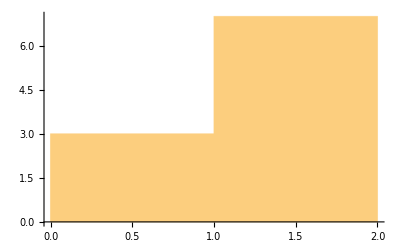

```mathematica
Histogram[randList]
```

{0,1,1,0,0,0,1,0,0,1}

{{0,6},{1,4}}

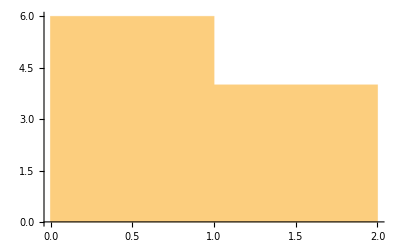

```mathematica
randList=RandomInteger[{0,1},10]
Tally[randList]
Histogram[randList]
```

```mathematica
randL
```

randL

```mathematica
randL=randList
```

{0,1,1,0,0,0,1,0,0,1}

```mathematica
randList={1,1,{1,2}}
```

{1,1,{1,2}}

```mathematica
Position[randList,1]
```

{{1},{2},{3,1}}

```mathematica
randList[[3,2]]
```

2

```mathematica
tau3
```

{{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}}

```mathematica
tau4
```

{{0.1,{0.59036,0.01,-2.28727},{0.92206,0.11,-3.7453},{0.75621,0.06,-3.01604}},{0.3,{0.531806,0.01,-2.02885},{0.826139,0.11,-3.39642},{0.973305,0.16,-4.08036},{0.973305,0.16,-4.08036}},{0.5,{0.484985,0.01,-1.82365},{0.747441,0.11,-3.11378},{0.878669,0.16,-3.75886},{0.878669,0.16,-3.75886}},{0.7,{0.446862,0.01,-1.65522},{0.681656,0.11,-2.87742},{0.916449,0.21,-4.09976},{0.916449,0.21,-4.09976}},{0.9,{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311},{0.836286,0.21,-3.8352},{0.836286,0.21,-3.8352},{0.94151,0.26,-4.41633}},{1.1,{0.38915,0.01,-1.38418},{0.577913,0.11,-2.49027},{0.766677,0.21,-3.59802},{0.95544,0.31,-4.70626},{0.861058,0.26,-4.15211}},{1.3,{0.367123,0.01,-1.26635},{0.536372,0.11,-2.3208},{0.705622,0.21,-3.37878},{0.874872,0.31,-4.43777},{0.959497,0.36,-4.96745}},{1.5,{0.348578,0.01,-246.3},{0.500106,0.11,-2.1583},{0.651633,0.21,-3.16998},{0.803161,0.31,-4.18351},{0.954688,0.41,-5.19787}}}

```mathematica
tau5={{0.1,{0.7296574674588863,0.01,-2.8414852887695763}},{0.30000000000000004,{0.6573996788950431,0.01,-2.513043246690493},{0.951731980550155,0.11,-3.8806510936954917}},{0.5,{0.5996702537827538,0.01,-2.249897260125059},{0.862125901611245,0.11,-3.5400266550493233}},{0.7,{0.5527080246309696,0.01,-2.0323512655731086},{0.78750131388657,0.11,-3.254553790697304}},{0.8999999999999999,{0.5139782963530029,0.01,-1.8462165850510004},{0.7244257406073074,0.11,-3.0076983370722603}},{1.0999999999999999,{0.4817179998428722,0.01,-1.68105727530624},{0.6704814753961298,0.11,-2.7871862659208957}},{1.2999999999999998,{0.4546720604176895,0.01,-1.5290027619808617},{0.623921766484159,0.11,-2.5836109056188596}},{1.4999999999999998,{0.43193445533774466,0.01,-1.3842606633722374},{0.5834619930647708,0.11,-2.3895468273010345}}}
```

{{0.1,{0.729657,0.01,-2.84149}},{0.3,{0.6574,0.01,-2.51304},{0.951732,0.11,-3.88065}},{0.5,{0.59967,0.01,-2.2499},{0.862126,0.11,-3.54003}},{0.7,{0.552708,0.01,-2.03235},{0.787501,0.11,-3.25455}},{0.9,{0.513978,0.01,-1.84622},{0.724426,0.11,-3.0077}},{1.1,{0.481718,0.01,-1.68106},{0.670481,0.11,-2.78719}},{1.3,{0.454672,0.01,-1.529},{0.623922,0.11,-2.58361}},{1.5,{0.431934,0.01,-1.38426},{0.583462,0.11,-2.38955}}}

```mathematica
tauList
```

{}

```mathematica
AppendTo[tauList,tau3];
AppendTo[tauList,tau4];
AppendTo[tauList,tau5];
```

```mathematica
tauList
tau
```

{{{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}},{{0.1,{0.59036,0.01,-2.28727},{0.92206,0.11,-3.7453},{0.75621,0.06,-3.01604}},{0.3,{0.531806,0.01,-2.02885},{0.826139,0.11,-3.39642},{0.973305,0.16,-4.08036},{0.973305,0.16,-4.08036}},{0.5,{0.484985,0.01,-1.82365},{0.747441,0.11,-3.11378},{0.878669,0.16,-3.75886},{0.878669,0.16,-3.75886}},{0.7,{0.446862,0.01,-1.65522},{0.681656,0.11,-2.87742},{0.916449,0.21,-4.09976},{0.916449,0.21,-4.09976}},{0.9,{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311},{0.836286,0.21,-3.8352},{0.836286,0.21,-3.8352},{0.94151,0.26,-4.41633}},{1.1,{0.38915,0.01,-1.38418},{0.577913,0.11,-2.49027},{0.766677,0.21,-3.59802},{0.95544,0.31,-4.70626},{0.861058,0.26,-4.15211}},{1.3,{0.367123,0.01,-1.26635},{0.536372,0.11,-2.3208},{0.705622,0.21,-3.37878},{0.874872,0.31,-4.43777},{0.959497,0.36,-4.96745}},{1.5,{0.348578,0.01,-246.3},{0.500106,0.11,-2.1583},{0.651633,0.21,-3.16998},{0.803161,0.31,-4.18351},{0.954688,0.41,-5.19787}}},{{0.1,{0.729657,0.01,-2.84149}},{0.3,{0.6574,0.01,-2.51304},{0.951732,0.11,-3.88065}},{0.5,{0.59967,0.01,-2.2499},{0.862126,0.11,-3.54003}},{0.7,{0.552708,0.01,-2.03235},{0.787501,0.11,-3.25455}},{0.9,{0.513978,0.01,-1.84622},{0.724426,0.11,-3.0077}},{1.1,{0.481718,0.01,-1.68106},{0.670481,0.11,-2.78719}},{1.3,{0.454672,0.01,-1.529},{0.623922,0.11,-2.58361}},{1.5,{0.431934,0.01,-1.38426},{0.583462,0.11,-2.38955}}}}

4

```mathematica
Length[tauList]
```

3

```mathematica
Position[tauList,3]
```

{}

```mathematica
Position[tauList,{3}]
```

{}

```mathematica
tau[[1]]
```

Part::partd: Part specification 4 ⟦ 1 ⟧ is longer than depth of object.

4⟦1⟧

```mathematica
tauList[[1]]
```

{{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}}

```mathematica
testList
```

{{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}},{2,{2.1,{2.111,2.112,2.113},{2.121,2.122,2.123}},{2.2,{2.211,2.212,2.213},{2.221,2.222,2.223}}}}

```mathematica
Position[testList,1]
```

{{1,1}}

```mathematica
tauData=Extract[testList,Extract[Flatten[Position[testList,1]],1]]
```

{1,{1.1,{1.111,1.112,1.113},{1.121,1.122,1.123}},{1.2,{1.211,1.212,1.213},{1.221,1.222,1.223}}}

```mathematica
desiredTau=1;
tauData=Extract[testList,Extract[Flatten[Position[testList,desiredTau]],1]];
plotData={};
For[i=2,i≤Length[tauData],i++,phiData=Extract[tauData,i];extractedPhi=Extract[phiData,1];
For[j=2,j≤Length[phiData],j++,plotSet={};actuatorData=Extract[phiData,j];AppendTo[plotSet,extractedPhi];AppendTo[plotSet,actuatorData[[2]]];AppendTo[plotSet,actuatorData[[3]]];AppendTo[plotData,plotSet]]]
plotData
```

{{1.1,1.112,1.113},{1.1,1.122,1.123},{1.2,1.212,1.213},{1.2,1.222,1.223}}

```mathematica
plotData
```

{{1.1,1.112,1.113},{1.1,1.122,1.123},{1.2,1.212,1.213},{1.2,1.222,1.223}}

```mathematica
ListPlot3D[plotData]
```

-Graphics3D-

```mathematica
tauList
```

{{{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}},{{0.1,{0.59036,0.01,-2.28727},{0.92206,0.11,-3.7453},{0.75621,0.06,-3.01604}},{0.3,{0.531806,0.01,-2.02885},{0.826139,0.11,-3.39642},{0.973305,0.16,-4.08036},{0.973305,0.16,-4.08036}},{0.5,{0.484985,0.01,-1.82365},{0.747441,0.11,-3.11378},{0.878669,0.16,-3.75886},{0.878669,0.16,-3.75886}},{0.7,{0.446862,0.01,-1.65522},{0.681656,0.11,-2.87742},{0.916449,0.21,-4.09976},{0.916449,0.21,-4.09976}},{0.9,{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311},{0.836286,0.21,-3.8352},{0.836286,0.21,-3.8352},{0.94151,0.26,-4.41633}},{1.1,{0.38915,0.01,-1.38418},{0.577913,0.11,-2.49027},{0.766677,0.21,-3.59802},{0.95544,0.31,-4.70626},{0.861058,0.26,-4.15211}},{1.3,{0.367123,0.01,-1.26635},{0.536372,0.11,-2.3208},{0.705622,0.21,-3.37878},{0.874872,0.31,-4.43777},{0.959497,0.36,-4.96745}},{1.5,{0.348578,0.01,-246.3},{0.500106,0.11,-2.1583},{0.651633,0.21,-3.16998},{0.803161,0.31,-4.18351},{0.954688,0.41,-5.19787}}},{{0.1,{0.729657,0.01,-2.84149}},{0.3,{0.6574,0.01,-2.51304},{0.951732,0.11,-3.88065}},{0.5,{0.59967,0.01,-2.2499},{0.862126,0.11,-3.54003}},{0.7,{0.552708,0.01,-2.03235},{0.787501,0.11,-3.25455}},{0.9,{0.513978,0.01,-1.84622},{0.724426,0.11,-3.0077}},{1.1,{0.481718,0.01,-1.68106},{0.670481,0.11,-2.78719}},{1.3,{0.454672,0.01,-1.529},{0.623922,0.11,-2.58361}},{1.5,{0.431934,0.01,-1.38426},{0.583462,0.11,-2.38955}}}}

```mathematica
PrependTo[tau3,3]
PrependTo[tau4,4]
PrependTo[tau5,5]
```

{3,{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}}

{4,{0.1,{0.59036,0.01,-2.28727},{0.92206,0.11,-3.7453},{0.75621,0.06,-3.01604}},{0.3,{0.531806,0.01,-2.02885},{0.826139,0.11,-3.39642},{0.973305,0.16,-4.08036},{0.973305,0.16,-4.08036}},{0.5,{0.484985,0.01,-1.82365},{0.747441,0.11,-3.11378},{0.878669,0.16,-3.75886},{0.878669,0.16,-3.75886}},{0.7,{0.446862,0.01,-1.65522},{0.681656,0.11,-2.87742},{0.916449,0.21,-4.09976},{0.916449,0.21,-4.09976}},{0.9,{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311},{0.836286,0.21,-3.8352},{0.836286,0.21,-3.8352},{0.94151,0.26,-4.41633}},{1.1,{0.38915,0.01,-1.38418},{0.577913,0.11,-2.49027},{0.766677,0.21,-3.59802},{0.95544,0.31,-4.70626},{0.861058,0.26,-4.15211}},{1.3,{0.367123,0.01,-1.26635},{0.536372,0.11,-2.3208},{0.705622,0.21,-3.37878},{0.874872,0.31,-4.43777},{0.959497,0.36,-4.96745}},{1.5,{0.348578,0.01,-246.3},{0.500106,0.11,-2.1583},{0.651633,0.21,-3.16998},{0.803161,0.31,-4.18351},{0.954688,0.41,-5.19787}}}

{5,{0.1,{0.729657,0.01,-2.84149}},{0.3,{0.6574,0.01,-2.51304},{0.951732,0.11,-3.88065}},{0.5,{0.59967,0.01,-2.2499},{0.862126,0.11,-3.54003}},{0.7,{0.552708,0.01,-2.03235},{0.787501,0.11,-3.25455}},{0.9,{0.513978,0.01,-1.84622},{0.724426,0.11,-3.0077}},{1.1,{0.481718,0.01,-1.68106},{0.670481,0.11,-2.78719}},{1.3,{0.454672,0.01,-1.529},{0.623922,0.11,-2.58361}},{1.5,{0.431934,0.01,-1.38426},{0.583462,0.11,-2.38955}}}

```mathematica
AppendTo[tauList,tau3];
AppendTo[tauList,tau4];
AppendTo[tauList,tau5];
```

```mathematica
tauList={}
```

{}

```mathematica
tauList
```

{{3,{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}},{4,{0.1,{0.59036,0.01,-2.28727},{0.92206,0.11,-3.7453},{0.75621,0.06,-3.01604}},{0.3,{0.531806,0.01,-2.02885},{0.826139,0.11,-3.39642},{0.973305,0.16,-4.08036},{0.973305,0.16,-4.08036}},{0.5,{0.484985,0.01,-1.82365},{0.747441,0.11,-3.11378},{0.878669,0.16,-3.75886},{0.878669,0.16,-3.75886}},{0.7,{0.446862,0.01,-1.65522},{0.681656,0.11,-2.87742},{0.916449,0.21,-4.09976},{0.916449,0.21,-4.09976}},{0.9,{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311},{0.836286,0.21,-3.8352},{0.836286,0.21,-3.8352},{0.94151,0.26,-4.41633}},{1.1,{0.38915,0.01,-1.38418},{0.577913,0.11,-2.49027},{0.766677,0.21,-3.59802},{0.95544,0.31,-4.70626},{0.861058,0.26,-4.15211}},{1.3,{0.367123,0.01,-1.26635},{0.536372,0.11,-2.3208},{0.705622,0.21,-3.37878},{0.874872,0.31,-4.43777},{0.959497,0.36,-4.96745}},{1.5,{0.348578,0.01,-246.3},{0.500106,0.11,-2.1583},{0.651633,0.21,-3.16998},{0.803161,0.31,-4.18351},{0.954688,0.41,-5.19787}}},{5,{0.1,{0.729657,0.01,-2.84149}},{0.3,{0.6574,0.01,-2.51304},{0.951732,0.11,-3.88065}},{0.5,{0.59967,0.01,-2.2499},{0.862126,0.11,-3.54003}},{0.7,{0.552708,0.01,-2.03235},{0.787501,0.11,-3.25455}},{0.9,{0.513978,0.01,-1.84622},{0.724426,0.11,-3.0077}},{1.1,{0.481718,0.01,-1.68106},{0.670481,0.11,-2.78719}},{1.3,{0.454672,0.01,-1.529},{0.623922,0.11,-2.58361}},{1.5,{0.431934,0.01,-1.38426},{0.583462,0.11,-2.38955}}}}

```mathematica
listPlotSet={};
For[desiredTau=3,desiredTau≤5,desiredTau++,
tauData=Extract[tauList,Extract[Flatten[Position[tauList,desiredTau]],1]];
plotData={};
For[i=2,i≤Length[tauData],i++,phiData=Extract[tauData,i];extractedPhi=Extract[phiData,1];
For[j=2,j≤Length[phiData],j++,plotSet={};actuatorData=Extract[phiData,j];AppendTo[plotSet,extractedPhi];AppendTo[plotSet,actuatorData[[2]]];AppendTo[plotSet,actuatorData[[3]]];AppendTo[plotData,plotSet]]];
AppendTo[listPlotSet,ListPlot3D[plotData]]]
Show[listPlotSet,PlotRange->All]
```

-Graphics3D-

```mathematica
Show[%241,ImageSize->Full]
```

-Graphics3D-

```mathematica
ListPlot3D[plotData,Mesh->Automatic,MeshFunctions->{#3&}]
```

-Graphics3D-

```mathematica
plotSet
```

{1.5,0.46,-5.47465}

```mathematica
randList
```

{1,1,{1,2}}

```mathematica
Show
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
listPlotSet
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
list
```

{{1}}

```mathematica
Quit
```

```mathematica
tauList
```

FindRoot::nlnum: The function value {{"BMJEC.position2.flange.tau"}[0.1]} is not a list of numbers with dimensions {1} at {t} = {0.1}.

ReplaceAll::reps: {FindRoot[tauFunction[t], {t, 0.1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {{"BMJEC.position2.flange.tau"}[1.]} is not a list of numbers with dimensions {1} at {t} = {1.}.

ReplaceAll::reps: {FindRoot[tauStiffnessFunction[t], {t, 1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {{"BMJEC.position2.flange.tau"}[1.]} is not a list of numbers with dimensions {1} at {t} = {1.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[tauStiffnessFunction[t], {t, 1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{{1,{0.1,{0.172467,0.01,-0.621507},{0.504167,0.11,-2.08069},{0.835867,0.21,-3.54061},{0.835867,0.21,-3.54061}},{0.3,{0.155027,0.01,-0.574929},{0.449359,0.11,-1.94322},{0.743691,0.21,-3.31147},{0.743691,0.21,-3.31147},{0.890857,0.26,-3.99559}},{0.5,{0.140931,0.01,-0.544637},{0.403386,0.11,-1.83492},{0.665842,0.21,-3.12518},{0.928297,0.31,-4.41541},{0.79707,0.26,-3.77029}},{0.7,{0.129325,0.01,-0.523248},{0.364118,0.11,-1.74582},{0.598912,0.21,-2.9683},{0.833705,0.31,-4.19075},{0.951102,0.36,-4.80196}},{0.9,{0.119631,0.01,-0.505741},{0.330079,0.11,-1.66868},{0.540526,0.21,-2.83125},{0.750974,0.31,-3.99378},{0.961421,0.41,-5.15629}},{1.1,{0.111445,0.01,-28.5955},{0.300208,0.11,-1.59807},{0.488972,0.21,-2.70689},{0.677735,0.31,-3.81567},{0.866499,0.41,-4.92447},{0.96088,0.46,-5.47885}},{1.3,{0.104474,0.01,-972.848},{0.273724,0.11,-1.52993},{0.442974,0.21,-2.58969},{0.612224,0.31,-3.64965},{0.781473,0.41,-4.70967},{0.950723,0.51,-5.76971}},{1.5,{0.0985091,0.01,-972.097},{0.250037,0.11,-1.46115},{0.401564,0.21,-2.47534},{0.553092,0.31,-3.49032},{0.704619,0.41,-4.50557},{0.856147,0.51,-5.52094}}},{2,{0.1,{0.311765,0.01,-1.17801},{0.643465,0.11,-2.63596},{0.975165,0.21,-4.0954},{0.975165,0.21,-4.0954}},{0.3,{0.28062,0.01,-1.0601},{0.574952,0.11,-2.42775},{0.869284,0.21,-3.79583},{0.869284,0.21,-3.79583}},{0.5,{0.255615,0.01,-0.971077},{0.518071,0.11,-2.26123},{0.780527,0.21,-3.55145},{0.780527,0.21,-3.55145},{0.911755,0.26,-4.19656}},{0.7,{0.235171,0.01,-0.900781},{0.469964,0.11,-2.12306},{0.704757,0.21,-3.34547},{0.939551,0.31,-4.5679},{0.822154,0.26,-3.95668}},{0.9,{0.218218,0.01,-0.841836},{0.428666,0.11,-2.00365},{0.639113,0.21,-3.16597},{0.84956,0.31,-4.32838},{0.954784,0.36,-4.90961}},{1.1,{0.204013,0.01,-0.789029},{0.392776,0.11,-1.89584},{0.58154,0.21,-3.00409},{0.770303,0.31,-4.11263},{0.959067,0.41,-5.22127}},{1.3,{0.192024,0.01,-245.984},{0.361274,0.11,-1.79414},{0.530523,0.21,-2.85298},{0.699773,0.31,-3.9125},{0.869023,0.41,-4.97227},{0.953647,0.46,-5.50221}},{1.5,{0.181865,0.01,-972.331},{0.333393,0.11,-1.69433},{0.484921,0.21,-2.70724},{0.636448,0.31,-3.72158},{0.787976,0.41,-4.73646},{0.939503,0.51,-5.75158}}},{3,{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}},{4,{0.1,{0.59036,0.01,-2.28727},{0.92206,0.11,-3.7453},{0.75621,0.06,-3.01604}},{0.3,{0.531806,0.01,-2.02885},{0.826139,0.11,-3.39642},{0.973305,0.16,-4.08036},{0.973305,0.16,-4.08036}},{0.5,{0.484985,0.01,-1.82365},{0.747441,0.11,-3.11378},{0.878669,0.16,-3.75886},{0.878669,0.16,-3.75886}},{0.7,{0.446862,0.01,-1.65522},{0.681656,0.11,-2.87742},{0.916449,0.21,-4.09976},{0.916449,0.21,-4.09976}},{0.9,{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311},{0.836286,0.21,-3.8352},{0.836286,0.21,-3.8352},{0.94151,0.26,-4.41633}},{1.1,{0.38915,0.01,-1.38418},{0.577913,0.11,-2.49027},{0.766677,0.21,-3.59802},{0.95544,0.31,-4.70626},{0.861058,0.26,-4.15211}},{1.3,{0.367123,0.01,-1.26635},{0.536372,0.11,-2.3208},{0.705622,0.21,-3.37878},{0.874872,0.31,-4.43777},{0.959497,0.36,-4.96745}},{1.5,{0.348578,0.01,-246.3},{0.500106,0.11,-2.1583},{0.651633,0.21,-3.16998},{0.803161,0.31,-4.18351},{0.954688,0.41,-5.19787}}},{5,{0.1,{0.729657,0.01,-2.84149},{0.729657,0.01,-2.84149},{0.895507,0.06,-3.57039}},{0.3,{0.6574,0.01,-2.51304},{0.951732,0.11,-3.88065},{0.804566,0.06,-3.19678}},{0.5,{0.59967,0.01,-2.2499},{0.862126,0.11,-3.54003},{0.993354,0.16,-4.18512},{0.993354,0.16,-4.18512}},{0.7,{0.552708,0.01,-2.03235},{0.787501,0.11,-3.25455},{0.904898,0.16,-3.86571},{0.904898,0.16,-3.86571}},{0.9,{0.513978,0.01,-1.84622},{0.724426,0.11,-3.0077},{0.934873,0.21,-4.16974},{0.934873,0.21,-4.16974}},{1.1,{0.481718,0.01,-1.68106},{0.670481,0.11,-2.78719},{0.859245,0.21,-3.89483},{0.859245,0.21,-3.89483},{0.953627,0.26,-4.44886}},{1.3,{0.454672,0.01,-1.529},{0.623922,0.11,-2.58361},{0.793171,0.21,-3.64141},{0.962421,0.31,-4.70025},{0.877796,0.26,-4.17075}},{1.5,{1/10 (t/.FindRoot[tauFunction[t],{t,0.1}]),0.01,({BMJEC.position2.flange.tau}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])/({BMJEC.position2.flange.phi}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])},{1/10 (t/.FindRoot[tauFunction[t],{t,0.1}]),0.11,({BMJEC.position2.flange.tau}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])/({BMJEC.position2.flange.phi}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])},{1/10 (t/.FindRoot[tauFunction[t],{t,0.1}]),0.21,({BMJEC.position2.flange.tau}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])/({BMJEC.position2.flange.phi}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])},{1/10 (t/.FindRoot[tauFunction[t],{t,0.1}]),0.31,({BMJEC.position2.flange.tau}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])/({BMJEC.position2.flange.phi}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])},{1/10 (t/.FindRoot[tauFunction[t],{t,0.1}]),0.41,({BMJEC.position2.flange.tau}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])/({BMJEC.position2.flange.phi}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])},{1/10 (t/.FindRoot[tauFunction[t],{t,0.1}]),0.51,({BMJEC.position2.flange.tau}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])/({BMJEC.position2.flange.phi}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])},{1/10 (t/.FindRoot[tauFunction[t],{t,0.1}]),0.61,({BMJEC.position2.flange.tau}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])/({BMJEC.position2.flange.phi}'[t/.FindRoot[tauStiffnessFunction[t],{t,1}]])}}}}

```mathematica
tauList={{1,{0.1,{0.17246748209778517,0.01,-0.6215071804315312},{0.5041673396728833,0.11,-2.0806936994440655},{0.8358671972479823,0.21000000000000002,-3.5406117215791193},{0.8358671972479823,0.21000000000000005,-3.5406117215791193}},{0.30000000000000004,{0.15502651991141775,0.01,-0.574929496901585},{0.4493588215665292,0.11,-1.943217544855483},{0.7436911232216428,0.21000000000000002,-3.3114682931815507},{0.7436911232216428,0.21000000000000005,-3.3114682931815507},{0.8908572740491976,0.26,-3.9955868757095567}},{0.5,{0.14093050258283002,0.01,-0.544637103707728},{0.40338615041132186,0.11,-1.8349225278704107},{0.6658417982398135,0.21000000000000002,-3.1251791448142607},{0.9282974460683051,0.31000000000000005,-4.415409116720823},{0.7970696221540581,0.26,-3.770288249589775}},{0.7,{0.129325068066642,0.01,-0.5232477661066292},{0.3641183573222426,0.11,-1.745824083645623},{0.5989116465778433,0.21000000000000002,-2.968300477808377},{0.8337049358334458,0.31000000000000005,-4.190750029494001},{0.9511015804612442,0.36000000000000004,-4.801957049958535}},{0.8999999999999999,{0.11963145481094484,0.01,-0.5057406421449807},{0.33007889906524857,0.11,-1.6686758803509845},{0.5405263433195535,0.21000000000000002,-2.8312488975415837},{0.7509737875738571,0.31000000000000005,-3.9937755795431644},{0.961421231828161,0.41000000000000003,-5.156289873662913}},{1.0999999999999999,{0.11144467801283503,0.01,-28.595540441986174},{0.3002081535660932,0.11,-1.5980723096690792},{0.48897162911935094,0.21000000000000002,-2.706887166168051},{0.6777351046726096,0.31000000000000005,-3.8156653680107535},{0.8664985802258661,0.41000000000000003,-4.92446948022156},{0.9608803180024955,0.46,-5.478850837207878}},{1.2999999999999998,{0.10447438856885552,0.01,-972.8484453014481},{0.2737240946353256,0.11,-1.5299304551231652},{0.4429738007017958,0.21000000000000002,-2.5896929622864344},{0.6122235067682658,0.31000000000000005,-3.6496517353486593},{0.7814732128347369,0.41000000000000003,-4.7096662674416105},{0.9507229189012059,0.51,-5.769710344590876}},{1.4999999999999998,{0.09850909408571104,0.01,-972.0973184120339},{0.2500366318127374,0.11,-1.4611518673737474},{0.40156416953976415,0.21000000000000002,-2.475340694648938},{0.55309170726679,0.31000000000000005,-3.490317550300232},{0.7046192449938172,0.41000000000000003,-4.5055663689502286},{0.8561467827208432,0.51,-5.520937756675159}}},{2,{0.1,{0.31176497843806045,0.01,-1.1780096345638444},{0.6434648360131588,0.11,-2.6359553622508107},{0.975164693588257,0.21000000000000002,-4.095403209113815},{0.975164693588257,0.21000000000000005,-4.095403209113815}},{0.30000000000000004,{0.28061980965732375,0.01,-1.060097095853091},{0.5749521113124353,0.11,-2.4277536819419696},{0.8692844129675508,0.21000000000000002,-3.795825476560629},{0.8692844129675508,0.21000000000000005,-3.795825476560629}},{0.5,{0.2556154403828108,0.01,-0.9710770679528483},{0.5180710882113023,0.11,-2.261233956546676},{0.7805267360397941,0.21000000000000002,-3.55145107265237},{0.7805267360397941,0.21000000000000005,-3.55145107265237},{0.9117545599540394,0.26,-4.196563064256439}},{0.7,{0.235170807207724,0.01,-0.9007813846119033},{0.46996409646332443,0.11,-2.1230634400251196},{0.704757385718927,0.21000000000000002,-3.345473916370003},{0.939550674974528,0.31000000000000005,-4.567895057348506},{0.8221540303467268,0.26,-3.956677345025464}},{0.8999999999999999,{0.21821816519645942,0.01,-0.8418363823815371},{0.4286656094507628,0.11,-2.0036527674174285},{0.6391130537050678,0.21000000000000002,-3.16597351165661},{0.8495604979593715,0.31000000000000005,-4.328383230727739},{0.9547842200865239,0.36000000000000004,-4.909607165717852}},{1.0999999999999999,{0.20401300847034398,0.01,-0.7890291689545762},{0.3927764840236019,0.11,-1.8958399509116703},{0.5815399595768603,0.21000000000000002,-3.004093851173624},{0.7703034351301188,0.31000000000000005,-4.112626001685086},{0.9590669106833754,0.41000000000000003,-5.221272499069757}},{1.2999999999999998,{0.19202380653106385,0.01,-245.98387114347042},{0.36127351259753404,0.11,-1.7941374233340814},{0.5305232186640048,0.21000000000000002,-2.85298230850327},{0.6997729247304744,0.31000000000000005,-3.9124971393846995},{0.8690226307969457,0.41000000000000003,-4.9722699720327475},{0.9536474838301796,0.46,-5.502205176041775}},{1.4999999999999998,{0.1818654343987195,0.01,-972.3311819709445},{0.3333929721257458,0.11,-1.6943332470562338},{0.4849205098527722,0.21000000000000002,-2.7072361250178356},{0.6364480475797983,0.31000000000000005,-3.7215774327280804},{0.7879755853068251,0.41000000000000003,-4.736455898671774},{0.9395031230338508,0.51,-5.751577094815849}}},{3,{0.1,{0.4510624747783354,0.01,-1.7328639393989451},{0.7827623323534354,0.11,-3.1907559275893465},{0.9486122611409833,0.16000000000000003,-3.920304428576725},{0.9486122611409833,0.16000000000000003,-3.920304428576725}},{0.30000000000000004,{0.40621309940323047,0.01,-1.5445715540353713},{0.7005454010583431,0.11,-2.912130864398997},{0.9948777027134558,0.21000000000000002,-4.280120764157873},{0.9948777027134558,0.21000000000000005,-4.280120764157873}},{0.5,{0.37030037818279204,0.01,-1.3973837426030518},{0.6327560260112837,0.11,-2.687506746994768},{0.8952116738397744,0.21000000000000002,-3.9777010089108105},{0.8952116738397744,0.21000000000000005,-3.9777010089108105}},{0.7,{0.34101654634880557,0.01,-1.278039761407753},{0.575809835604406,0.11,-2.5002599544168813},{0.8106031248600089,0.21000000000000002,-3.7226204168753987},{0.8106031248600089,0.21000000000000005,-3.7226204168753987},{0.9279997694878077,0.26,-4.333818798692357}},{0.8999999999999999,{0.31680487558197384,0.01,-1.1769096483328543},{0.5272523198362778,0.11,-2.3384417720165107},{0.7376997640905829,0.21000000000000002,-3.5006199000968103},{0.9481472083448858,0.31000000000000005,-4.662955258627991},{0.8429234862177339,0.26,-4.081771733411182}},{1.0999999999999999,{0.29658133892785327,0.01,-1.0869774970804011},{0.485344814481111,0.11,-2.193183872881259},{0.6741082900343693,0.21000000000000002,-3.301126008315924},{0.8628717655876281,0.31000000000000005,-4.409481893814092},{0.9572535033642565,0.36000000000000004,-4.9637322634259675}},{1.2999999999999998,{0.27957322449327193,0.01,-1.0031445113313144},{0.4488229305597427,0.11,-2.0576819308940832},{0.6180726366262126,0.21000000000000002,-3.1159817018606053},{0.7873223426926833,0.31000000000000005,-4.175199637268605},{0.9565720487591535,0.41000000000000003,-5.234777219621499}},{1.4999999999999998,{0.26522177471172775,0.01,2553.1278255936036},{0.4167493124387538,0.11,-1.92663120187879},{0.5682768501657807,0.21000000000000002,-2.938747812939917},{0.7198043878928075,0.31000000000000005,-3.9526335453036157},{0.8713319256198331,0.41000000000000003,-4.967221268297658},{0.9470956944833461,0.46,-5.474645694447102}}},{4,{0.1,{0.5903599711186108,0.01,-2.287273667614084},{0.92205982869371,0.11,-3.74529933561837},{0.7562098999061599,0.060000000000000026,-3.0160382578529035}},{0.30000000000000004,{0.5318063891491369,0.01,-2.028849439472903},{0.8261386908042498,0.11,-3.396419689219262},{0.9733048416318045,0.16000000000000003,-4.080362601209058},{0.9733048416318045,0.16000000000000003,-4.080362601209058}},{0.5,{0.4849853159827734,0.01,-1.8236516277172274},{0.7474409638112642,0.11,-3.113776656835997},{0.878668787725509,0.16000000000000003,-3.758863831704731},{0.878668787725509,0.16000000000000003,-3.758863831704731}},{0.7,{0.44686228548988716,0.01,-1.6552159277873504},{0.6816555747454884,0.11,-2.877416031985864},{0.9164488640010906,0.21000000000000002,-4.0997646911127354},{0.9164488640010906,0.21000000000000005,-4.0997646911127354}},{0.8999999999999999,{0.41539158596748876,0.01,-1.5116446374642822},{0.6258390302217922,0.11,-2.673110330713452},{0.8362864744760978,0.21000000000000002,-3.8352028488745975},{0.8362864744760978,0.21000000000000005,-3.8352028488745975},{0.9415101966032469,0.26,-4.416328715697791}},{1.0999999999999999,{0.38914966938536266,0.01,-1.3841823187081481},{0.5779131449386198,0.11,-2.4902691643583124},{0.7666766204918791,0.21000000000000002,-3.5980238193124694},{0.9554400960451361,0.31000000000000005,-4.706258919828654},{0.8610583582685092,0.26,-4.152105088852784}},{1.2999999999999998,{0.3671226424554812,0.01,-1.26635297317119},{0.5363723485219506,0.11,-2.320801642486794},{0.7056220545884209,0.21000000000000002,-3.3787789491430438},{0.8748717606548919,0.31000000000000005,-4.437766749578259},{0.9594966136881262,0.36000000000000004,-4.967453046805157}},{1.4999999999999998,{0.3485781150247367,0.01,-246.3001023490395},{0.5001056527517623,0.11,-2.1583034809812243},{0.6516331904787891,0.21000000000000002,-3.1699754740695574},{0.8031607282058165,0.31000000000000005,-4.183511493423051},{0.9546882659328422,0.41000000000000003,-5.1978686792108055}}},{5,{0.1,{0.7296574674588863,0.01,-2.8414852887695763},{0.7296574674588863,0.009999999999999995,-2.8414852887695763},{0.8955073962464364,0.06,-3.5703913624190586}},{0.30000000000000004,{0.6573996788950431,0.01,-2.513043246690493},{0.951731980550155,0.11,-3.8806510936954917},{0.8045658297225979,0.060000000000000026,-3.1967823850113284}},{0.5,{0.5996702537827538,0.01,-2.249897260125059},{0.862125901611245,0.11,-3.5400266550493233},{0.9933537255254898,0.16000000000000003,-4.185116717874599},{0.9933537255254898,0.16000000000000003,-4.185116717874599}},{0.7,{0.5527080246309696,0.01,-2.0323512655731086},{0.78750131388657,0.11,-3.254553790697304},{0.9048979585143706,0.16000000000000003,-3.8657120746425724},{0.9048979585143706,0.16000000000000003,-3.8657120746425724}},{0.8999999999999999,{0.5139782963530029,0.01,-1.8462165850510004},{0.7244257406073074,0.11,-3.0076983370722603},{0.93487318486161,0.21000000000000002,-4.169744779094946},{0.93487318486161,0.21000000000000005,-4.169744779094946}},{1.0999999999999999,{0.4817179998428722,0.01,-1.68105727530624},{0.6704814753961298,0.11,-2.7871862659208957},{0.8592449509493882,0.21000000000000002,-3.894830314471017},{0.8592449509493882,0.21000000000000005,-3.894830314471017},{0.9536266887260173,0.26,-4.448863244600853}},{1.2999999999999998,{0.4546720604176895,0.01,-1.5290027619808617},{0.623921766484159,0.11,-2.5836109056188596},{0.7931714725506289,0.21000000000000002,-3.641413999143726},{0.9624211786170996,0.31000000000000005,-4.700250581432937},{0.8777963255838648,0.26,-4.170753605370416}}}}
```

{{1,{0.1,{0.172467,0.01,-0.621507},{0.504167,0.11,-2.08069},{0.835867,0.21,-3.54061},{0.835867,0.21,-3.54061}},{0.3,{0.155027,0.01,-0.574929},{0.449359,0.11,-1.94322},{0.743691,0.21,-3.31147},{0.743691,0.21,-3.31147},{0.890857,0.26,-3.99559}},{0.5,{0.140931,0.01,-0.544637},{0.403386,0.11,-1.83492},{0.665842,0.21,-3.12518},{0.928297,0.31,-4.41541},{0.79707,0.26,-3.77029}},{0.7,{0.129325,0.01,-0.523248},{0.364118,0.11,-1.74582},{0.598912,0.21,-2.9683},{0.833705,0.31,-4.19075},{0.951102,0.36,-4.80196}},{0.9,{0.119631,0.01,-0.505741},{0.330079,0.11,-1.66868},{0.540526,0.21,-2.83125},{0.750974,0.31,-3.99378},{0.961421,0.41,-5.15629}},{1.1,{0.111445,0.01,-28.5955},{0.300208,0.11,-1.59807},{0.488972,0.21,-2.70689},{0.677735,0.31,-3.81567},{0.866499,0.41,-4.92447},{0.96088,0.46,-5.47885}},{1.3,{0.104474,0.01,-972.848},{0.273724,0.11,-1.52993},{0.442974,0.21,-2.58969},{0.612224,0.31,-3.64965},{0.781473,0.41,-4.70967},{0.950723,0.51,-5.76971}},{1.5,{0.0985091,0.01,-972.097},{0.250037,0.11,-1.46115},{0.401564,0.21,-2.47534},{0.553092,0.31,-3.49032},{0.704619,0.41,-4.50557},{0.856147,0.51,-5.52094}}},{2,{0.1,{0.311765,0.01,-1.17801},{0.643465,0.11,-2.63596},{0.975165,0.21,-4.0954},{0.975165,0.21,-4.0954}},{0.3,{0.28062,0.01,-1.0601},{0.574952,0.11,-2.42775},{0.869284,0.21,-3.79583},{0.869284,0.21,-3.79583}},{0.5,{0.255615,0.01,-0.971077},{0.518071,0.11,-2.26123},{0.780527,0.21,-3.55145},{0.780527,0.21,-3.55145},{0.911755,0.26,-4.19656}},{0.7,{0.235171,0.01,-0.900781},{0.469964,0.11,-2.12306},{0.704757,0.21,-3.34547},{0.939551,0.31,-4.5679},{0.822154,0.26,-3.95668}},{0.9,{0.218218,0.01,-0.841836},{0.428666,0.11,-2.00365},{0.639113,0.21,-3.16597},{0.84956,0.31,-4.32838},{0.954784,0.36,-4.90961}},{1.1,{0.204013,0.01,-0.789029},{0.392776,0.11,-1.89584},{0.58154,0.21,-3.00409},{0.770303,0.31,-4.11263},{0.959067,0.41,-5.22127}},{1.3,{0.192024,0.01,-245.984},{0.361274,0.11,-1.79414},{0.530523,0.21,-2.85298},{0.699773,0.31,-3.9125},{0.869023,0.41,-4.97227},{0.953647,0.46,-5.50221}},{1.5,{0.181865,0.01,-972.331},{0.333393,0.11,-1.69433},{0.484921,0.21,-2.70724},{0.636448,0.31,-3.72158},{0.787976,0.41,-4.73646},{0.939503,0.51,-5.75158}}},{3,{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}},{4,{0.1,{0.59036,0.01,-2.28727},{0.92206,0.11,-3.7453},{0.75621,0.06,-3.01604}},{0.3,{0.531806,0.01,-2.02885},{0.826139,0.11,-3.39642},{0.973305,0.16,-4.08036},{0.973305,0.16,-4.08036}},{0.5,{0.484985,0.01,-1.82365},{0.747441,0.11,-3.11378},{0.878669,0.16,-3.75886},{0.878669,0.16,-3.75886}},{0.7,{0.446862,0.01,-1.65522},{0.681656,0.11,-2.87742},{0.916449,0.21,-4.09976},{0.916449,0.21,-4.09976}},{0.9,{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311},{0.836286,0.21,-3.8352},{0.836286,0.21,-3.8352},{0.94151,0.26,-4.41633}},{1.1,{0.38915,0.01,-1.38418},{0.577913,0.11,-2.49027},{0.766677,0.21,-3.59802},{0.95544,0.31,-4.70626},{0.861058,0.26,-4.15211}},{1.3,{0.367123,0.01,-1.26635},{0.536372,0.11,-2.3208},{0.705622,0.21,-3.37878},{0.874872,0.31,-4.43777},{0.959497,0.36,-4.96745}},{1.5,{0.348578,0.01,-246.3},{0.500106,0.11,-2.1583},{0.651633,0.21,-3.16998},{0.803161,0.31,-4.18351},{0.954688,0.41,-5.19787}}},{5,{0.1,{0.729657,0.01,-2.84149},{0.729657,0.01,-2.84149},{0.895507,0.06,-3.57039}},{0.3,{0.6574,0.01,-2.51304},{0.951732,0.11,-3.88065},{0.804566,0.06,-3.19678}},{0.5,{0.59967,0.01,-2.2499},{0.862126,0.11,-3.54003},{0.993354,0.16,-4.18512},{0.993354,0.16,-4.18512}},{0.7,{0.552708,0.01,-2.03235},{0.787501,0.11,-3.25455},{0.904898,0.16,-3.86571},{0.904898,0.16,-3.86571}},{0.9,{0.513978,0.01,-1.84622},{0.724426,0.11,-3.0077},{0.934873,0.21,-4.16974},{0.934873,0.21,-4.16974}},{1.1,{0.481718,0.01,-1.68106},{0.670481,0.11,-2.78719},{0.859245,0.21,-3.89483},{0.859245,0.21,-3.89483},{0.953627,0.26,-4.44886}},{1.3,{0.454672,0.01,-1.529},{0.623922,0.11,-2.58361},{0.793171,0.21,-3.64141},{0.962421,0.31,-4.70025},{0.877796,0.26,-4.17075}}}}

```mathematica
listPlotSet={};
For[desiredTau=1,desiredTau≤5,desiredTau++,
tauData=Extract[tauList,Extract[Flatten[Position[tauList,desiredTau]],1]];
plotData={};
For[i=2,i≤Length[tauData],i++,phiData=Extract[tauData,i];extractedPhi=Extract[phiData,1];
For[j=2,j≤Length[phiData],j++,plotSet={};actuatorData=Extract[phiData,j];AppendTo[plotSet,extractedPhi];AppendTo[plotSet,actuatorData[[3]]];
AppendTo[plotSet,actuatorData[[2]]];
AppendTo[plotData,plotSet]]];
AppendTo[listPlotSet,ListPlot3D[plotData]]]
Show[listPlotSet,PlotRange->All]
```

-Graphics3D-

```mathematica
Show[%21,ImageSize->Full]
```

-Graphics3D-

```mathematica
Show[%22,AxesStyle->Black]
```

-Graphics3D-

```mathematica
Show[%23,AxesStyle->Gray]
```

-Graphics3D-

```mathematica
Show[%24,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Show[%24,AxesStyle->White]
```

-Graphics3D-

```mathematica
Show[%5,ImageSize->Full]
```

-Graphics3D-

```mathematica
negTauList={{-5,{0.1,{0.3317820767814267,0.31000000000000005,-1.6639933240371774},{0.6634819343565242,0.41000000000000003,-3.1300698357309535},{0.9951817919316215,0.51,-4.592283544742565}},{0.30000000000000004,{0.28446368640131664,0.31000000000000005,-1.7714491969835497},{0.578795988056429,0.41000000000000003,-3.1413410846074097},{0.8731282897115415,0.51,-4.510220354947344}},{0.5,{0.24018781926841967,0.31000000000000005,-1.8574643281967609},{0.5026434670969113,0.41000000000000003,-3.1479841212170983},{0.7650991149254025,0.51,-4.438301809753176}},{0.7,{0.19863050098695334,0.31000000000000005,-1.9272290091978295},{0.43342379024255434,0.41000000000000003,-3.150128915195075},{0.6682170794981546,0.51,-4.372720706236548},{0.9030103687537565,0.61,-5.595295916763282}},{0.8999999999999999,{0.15945352526077067,0.31000000000000005,-1.9839448717997552},{0.369900969515075,0.41000000000000003,-3.1479833739215395},{0.5803484137693798,0.51,-4.3111449141269045},{0.790795858023684,0.61,-5.474062350075463}},{1.0999999999999999,{0.1223251219275537,0.31000000000000005,-2.0297978850306166},{0.3110885974808113,0.41000000000000003,-3.1415024576981696},{0.4998520730340694,0.51,-4.251718875806138},{0.6886155485873272,0.61,-5.361313582106019}},{1.2999999999999998,{0.08692699899501567,0.31000000000000005,-2.0661437325975838},{0.2561767050614857,0.41000000000000003,-3.130743227640145},{0.42542641112795654,0.51,-4.1930249396235935},{0.5946761171944258,0.61,-5.25447905112443}},{1.4999999999999998,{0.05295366538873977,0.31000000000000005,-2.0943355724645443},{0.20448120311576617,0.41000000000000003,-3.115722713634184},{0.35600874084279244,0.51,-4.1342835374809965},{0.5075362785698192,0.61,-5.151625971210121}}},{-4,{0.1,{0.13937971554660405,0.21000000000000002,-0.7471154961623399},{0.4710795731217027,0.31000000000000005,-2.2228019893691062},{0.8027794306968018,0.41000000000000003,-3.6860306262291482},{0.9686293594843485,0.46,-4.416864950443287}},{0.30000000000000004,{0.1157246744921104,0.21000000000000002,-0.8847108120769585},{0.4100569761472227,0.31000000000000005,-2.2568825537485893},{0.7043892778023352,0.41000000000000003,-3.626028211832066},{0.9987215794574479,0.51,-4.994671663638978}},{0.5,{0.09241710923990876,0.21000000000000002,-0.9931376336514958},{0.354872757068401,0.31000000000000005,-2.2839073496608036},{0.6173284048968926,0.41000000000000003,-3.5742999077207958},{0.8797840527253835,0.51,-4.864547569152758}},{0.7,{0.0696829508724345,0.21000000000000002,-1.0812723730692166},{0.3044762401280355,0.31000000000000005,-2.304608221388703},{0.5392695293836359,0.41000000000000003,-3.527324185395419},{0.7740628186392375,0.51,-4.749905869250694}},{0.8999999999999999,{0.04759279139198095,0.21000000000000002,-1.1539599404032537},{0.2580402356462852,0.31000000000000005,-2.319407983577804},{0.46848767990058926,0.41000000000000003,-3.4828749801544774},{0.6789351241548928,0.51,-4.645883988781364},{0.8893825684091992,0.61,-5.80865816745721}},{1.0999999999999999,{0.026129976831804708,0.21000000000000002,-1.2139828227503684},{0.21489345238506274,0.31000000000000005,-2.3283183116302446},{0.4036569279383204,0.41000000000000003,-3.43906824897735},{0.5924204034915785,0.51,-4.548873485860476},{0.7811838790448365,0.61,-5.658245523167121}},{1.2999999999999998,{0.17447641695722402,0.31000000000000005,-2.331344528915889},{0.3437261230236942,0.41000000000000003,-3.394456795157292},{0.5129758290901644,0.51,-4.456171665207347},{0.682225535156634,0.61,-5.51724877665806}},{1.4999999999999998,{0.13631000570174814,0.31000000000000005,-2.3286000677257146},{0.2878375434287747,0.41000000000000003,-3.348119399577283},{0.4393650811558003,0.51,-4.3657963936990525},{0.5908926188828275,0.61,-5.382707849820644}}},{-3,{0.1,{0.27867721188687966,0.21000000000000002,-1.3139742231073395},{0.6103770694619793,0.31000000000000005,-2.77968204990517},{0.9420769270370777,0.41000000000000003,-4.241517566088616}},{0.30000000000000004,{0.24131796423801652,0.21000000000000002,-1.3718855481405348},{0.5356502658931294,0.31000000000000005,-2.7417702336588157},{0.829982567548242,0.41000000000000003,-4.110596393039242},{0.9771487183757991,0.46,-4.794820298510944}},{0.5,{0.20710204703988966,0.21000000000000002,-1.4197500711967024},{0.4695576948683816,0.31000000000000005,-2.710224001916416},{0.7320133426968739,0.41000000000000003,-4.000549844125786},{0.9944689905253633,0.51,-5.290862564831272}},{0.7,{0.17552869001351626,0.21000000000000002,-1.4590288904693878},{0.4103219792691178,0.31000000000000005,-2.6819484840544554},{0.6451152685247182,0.41000000000000003,-3.904561663370817},{0.8799085577803201,0.51,-5.127082425531736}},{0.8999999999999999,{0.14617950177749542,0.21000000000000002,-1.4904465371636444},{0.3566269460317999,0.31000000000000005,-2.654577096752612},{0.5670743902861034,0.41000000000000003,-3.8177139455979097},{0.7775218345404071,0.51,-4.9805402228036915},{0.9879692787947122,0.61,-6.143236156007214}},{1.0999999999999999,{0.11869830728931388,0.21000000000000002,-1.5143793279772433},{0.30746178284257203,0.31000000000000005,-2.6263244348479016},{0.4962252583958302,0.41000000000000003,-3.7364177250519526},{0.6849887339490868,0.51,-4.845875141102672},{0.8737522095023458,0.61,-5.955126397574896}},{1.2999999999999998,{0.09277612885296208,0.21000000000000002,-1.5309765076455428},{0.2620258349194324,0.31000000000000005,-2.5958166962814673},{0.43127554098590287,0.41000000000000003,-3.6579016809857277},{0.6005252470523726,0.51,-4.719111357162109},{0.7697749531188424,0.61,-5.779916097164032}},{1.4999999999999998,{0.06813880828772996,0.21000000000000002,-1.5404165138267167},{0.21966634601475668,0.31000000000000005,-2.5619975518302622},{0.3711938837417832,0.41000000000000003,-3.5801504724547635},{0.5227214214688093,0.51,-4.597146644853168},{0.6742489591958356,0.61,-5.6136597968190305}}}}
```

{{-5,{0.1,{0.331782,0.31,-1.66399},{0.663482,0.41,-3.13007},{0.995182,0.51,-4.59228}},{0.3,{0.284464,0.31,-1.77145},{0.578796,0.41,-3.14134},{0.873128,0.51,-4.51022}},{0.5,{0.240188,0.31,-1.85746},{0.502643,0.41,-3.14798},{0.765099,0.51,-4.4383}},{0.7,{0.198631,0.31,-1.92723},{0.433424,0.41,-3.15013},{0.668217,0.51,-4.37272},{0.90301,0.61,-5.5953}},{0.9,{0.159454,0.31,-1.98394},{0.369901,0.41,-3.14798},{0.580348,0.51,-4.31114},{0.790796,0.61,-5.47406}},{1.1,{0.122325,0.31,-2.0298},{0.311089,0.41,-3.1415},{0.499852,0.51,-4.25172},{0.688616,0.61,-5.36131}},{1.3,{0.086927,0.31,-2.06614},{0.256177,0.41,-3.13074},{0.425426,0.51,-4.19302},{0.594676,0.61,-5.25448}},{1.5,{0.0529537,0.31,-2.09434},{0.204481,0.41,-3.11572},{0.356009,0.51,-4.13428},{0.507536,0.61,-5.15163}}},{-4,{0.1,{0.13938,0.21,-0.747115},{0.47108,0.31,-2.2228},{0.802779,0.41,-3.68603},{0.968629,0.46,-4.41686}},{0.3,{0.115725,0.21,-0.884711},{0.410057,0.31,-2.25688},{0.704389,0.41,-3.62603},{0.998722,0.51,-4.99467}},{0.5,{0.0924171,0.21,-0.993138},{0.354873,0.31,-2.28391},{0.617328,0.41,-3.5743},{0.879784,0.51,-4.86455}},{0.7,{0.069683,0.21,-1.08127},{0.304476,0.31,-2.30461},{0.53927,0.41,-3.52732},{0.774063,0.51,-4.74991}},{0.9,{0.0475928,0.21,-1.15396},{0.25804,0.31,-2.31941},{0.468488,0.41,-3.48287},{0.678935,0.51,-4.64588},{0.889383,0.61,-5.80866}},{1.1,{0.02613,0.21,-1.21398},{0.214893,0.31,-2.32832},{0.403657,0.41,-3.43907},{0.59242,0.51,-4.54887},{0.781184,0.61,-5.65825}},{1.3,{0.174476,0.31,-2.33134},{0.343726,0.41,-3.39446},{0.512976,0.51,-4.45617},{0.682226,0.61,-5.51725}},{1.5,{0.13631,0.31,-2.3286},{0.287838,0.41,-3.34812},{0.439365,0.51,-4.3658},{0.590893,0.61,-5.38271}}},{-3,{0.1,{0.278677,0.21,-1.31397},{0.610377,0.31,-2.77968},{0.942077,0.41,-4.24152}},{0.3,{0.241318,0.21,-1.37189},{0.53565,0.31,-2.74177},{0.829983,0.41,-4.1106},{0.977149,0.46,-4.79482}},{0.5,{0.207102,0.21,-1.41975},{0.469558,0.31,-2.71022},{0.732013,0.41,-4.00055},{0.994469,0.51,-5.29086}},{0.7,{0.175529,0.21,-1.45903},{0.410322,0.31,-2.68195},{0.645115,0.41,-3.90456},{0.879909,0.51,-5.12708}},{0.9,{0.14618,0.21,-1.49045},{0.356627,0.31,-2.65458},{0.567074,0.41,-3.81771},{0.777522,0.51,-4.98054},{0.987969,0.61,-6.14324}},{1.1,{0.118698,0.21,-1.51438},{0.307462,0.31,-2.62632},{0.496225,0.41,-3.73642},{0.684989,0.51,-4.84588},{0.873752,0.61,-5.95513}},{1.3,{0.0927761,0.21,-1.53098},{0.262026,0.31,-2.59582},{0.431276,0.41,-3.6579},{0.600525,0.51,-4.71911},{0.769775,0.61,-5.77992}},{1.5,{0.0681388,0.21,-1.54042},{0.219666,0.31,-2.562},{0.371194,0.41,-3.58015},{0.522721,0.51,-4.59715},{0.674249,0.61,-5.61366}}}}

```mathematica
negfintauList
```

{{-2,{0.1,{0.0862749,0.11,-0.392672},{0.417975,0.21,-1.87304},{0.749675,0.31,-3.33553},{0.915524,0.36,-4.06617}},{0.3,{0.072579,0.11,-0.483969},{0.366911,0.21,-1.85744},{0.661244,0.31,-3.22647},{0.955576,0.41,-4.59499}},{0.5,{0.0593313,0.11,-0.555233},{0.321787,0.21,-1.84619},{0.584243,0.31,-3.13658},{0.846698,0.41,-4.42686},{0.977926,0.46,-5.07201}},{0.7,{0.0465811,0.11,-0.612821},{0.281374,0.21,-1.83651},{0.516168,0.31,-3.05919},{0.750961,0.41,-4.28174},{0.985754,0.51,-5.50425}},{0.9,{0.0343188,0.11,-0.659612},{0.244766,0.21,-1.82615},{0.455214,0.31,-2.98954},{0.665661,0.41,-4.15242},{0.876109,0.51,-5.31517}},{1.1,{0.0225032,0.11,-0.697116},{0.211267,0.21,-1.81342},{0.40003,0.31,-2.92402},{0.588794,0.41,-4.0336},{0.777557,0.51,-5.14282},{0.966321,0.61,-6.25189}},{1.3,{0.0110758,0.11,-245.976},{0.180326,0.21,-1.797},{0.349575,0.31,-2.85976},{0.518825,0.41,-3.92111},{0.688075,0.51,-4.9819},{0.857324,0.61,-6.04247}},{1.5,{0.151495,0.21,-1.77582},{0.303023,0.31,-2.79473},{0.45455,0.41,-3.81186},{0.606078,0.51,-4.82831},{0.757605,0.61,-5.84448}}},{-1,{0.1,{0.225572,0.11,-0.965565},{0.557272,0.21,-2.42978},{0.888972,0.31,-3.89091},{0.723122,0.26,-3.16045}},{0.3,{0.198172,0.11,-0.97275},{0.492505,0.21,-2.34237},{0.786837,0.31,-3.71095},{0.934003,0.36,-4.39518}},{0.5,{0.174016,0.11,-0.982085},{0.436472,0.21,-2.27257},{0.698928,0.31,-3.56288},{0.961383,0.41,-4.8531}},{0.7,{0.152427,0.11,-0.990947},{0.38722,0.21,-2.21384},{0.622013,0.31,-3.4364},{0.856807,0.41,-4.6589},{0.974203,0.46,-5.27013}},{0.9,{0.132905,0.11,-0.997333},{0.343353,0.21,-2.1614},{0.5538,0.31,-3.32437},{0.764248,0.41,-4.4871},{0.974695,0.51,-5.64973}},{1.1,{0.115071,0.11,-0.999871},{0.303835,0.21,-2.1117},{0.492598,0.31,-3.2214},{0.681362,0.41,-4.33064},{0.870125,0.51,-5.4397}},{1.3,{0.0986253,0.11,-0.997489},{0.267875,0.21,-2.06189},{0.437125,0.31,-3.12334},{0.606374,0.41,-4.18411},{0.775624,0.51,-5.24461},{0.944874,0.61,-6.30497}},{1.5,{0.083324,0.11,-972.641},{0.234851,0.21,-2.00985},{0.386379,0.31,-3.02696},{0.537907,0.41,-4.0433},{0.689434,0.51,-5.05931},{0.840962,0.61,-6.0752}}}}

```mathematica
negTauList
```

{{-5,{0.1,{0.331782,0.31,-1.66399},{0.663482,0.41,-3.13007},{0.995182,0.51,-4.59228}},{0.3,{0.284464,0.31,-1.77145},{0.578796,0.41,-3.14134},{0.873128,0.51,-4.51022}},{0.5,{0.240188,0.31,-1.85746},{0.502643,0.41,-3.14798},{0.765099,0.51,-4.4383}},{0.7,{0.198631,0.31,-1.92723},{0.433424,0.41,-3.15013},{0.668217,0.51,-4.37272},{0.90301,0.61,-5.5953}},{0.9,{0.159454,0.31,-1.98394},{0.369901,0.41,-3.14798},{0.580348,0.51,-4.31114},{0.790796,0.61,-5.47406}},{1.1,{0.122325,0.31,-2.0298},{0.311089,0.41,-3.1415},{0.499852,0.51,-4.25172},{0.688616,0.61,-5.36131}},{1.3,{0.086927,0.31,-2.06614},{0.256177,0.41,-3.13074},{0.425426,0.51,-4.19302},{0.594676,0.61,-5.25448}},{1.5,{0.0529537,0.31,-2.09434},{0.204481,0.41,-3.11572},{0.356009,0.51,-4.13428},{0.507536,0.61,-5.15163}}},{-4,{0.1,{0.13938,0.21,-0.747115},{0.47108,0.31,-2.2228},{0.802779,0.41,-3.68603},{0.968629,0.46,-4.41686}},{0.3,{0.115725,0.21,-0.884711},{0.410057,0.31,-2.25688},{0.704389,0.41,-3.62603},{0.998722,0.51,-4.99467}},{0.5,{0.0924171,0.21,-0.993138},{0.354873,0.31,-2.28391},{0.617328,0.41,-3.5743},{0.879784,0.51,-4.86455}},{0.7,{0.069683,0.21,-1.08127},{0.304476,0.31,-2.30461},{0.53927,0.41,-3.52732},{0.774063,0.51,-4.74991}},{0.9,{0.0475928,0.21,-1.15396},{0.25804,0.31,-2.31941},{0.468488,0.41,-3.48287},{0.678935,0.51,-4.64588},{0.889383,0.61,-5.80866}},{1.1,{0.02613,0.21,-1.21398},{0.214893,0.31,-2.32832},{0.403657,0.41,-3.43907},{0.59242,0.51,-4.54887},{0.781184,0.61,-5.65825}},{1.3,{0.174476,0.31,-2.33134},{0.343726,0.41,-3.39446},{0.512976,0.51,-4.45617},{0.682226,0.61,-5.51725}},{1.5,{0.13631,0.31,-2.3286},{0.287838,0.41,-3.34812},{0.439365,0.51,-4.3658},{0.590893,0.61,-5.38271}}},{-3,{0.1,{0.278677,0.21,-1.31397},{0.610377,0.31,-2.77968},{0.942077,0.41,-4.24152}},{0.3,{0.241318,0.21,-1.37189},{0.53565,0.31,-2.74177},{0.829983,0.41,-4.1106},{0.977149,0.46,-4.79482}},{0.5,{0.207102,0.21,-1.41975},{0.469558,0.31,-2.71022},{0.732013,0.41,-4.00055},{0.994469,0.51,-5.29086}},{0.7,{0.175529,0.21,-1.45903},{0.410322,0.31,-2.68195},{0.645115,0.41,-3.90456},{0.879909,0.51,-5.12708}},{0.9,{0.14618,0.21,-1.49045},{0.356627,0.31,-2.65458},{0.567074,0.41,-3.81771},{0.777522,0.51,-4.98054},{0.987969,0.61,-6.14324}},{1.1,{0.118698,0.21,-1.51438},{0.307462,0.31,-2.62632},{0.496225,0.41,-3.73642},{0.684989,0.51,-4.84588},{0.873752,0.61,-5.95513}},{1.3,{0.0927761,0.21,-1.53098},{0.262026,0.31,-2.59582},{0.431276,0.41,-3.6579},{0.600525,0.51,-4.71911},{0.769775,0.61,-5.77992}},{1.5,{0.0681388,0.21,-1.54042},{0.219666,0.31,-2.562},{0.371194,0.41,-3.58015},{0.522721,0.51,-4.59715},{0.674249,0.61,-5.61366}}}}

```mathematica
Append[{},{{1}}]
```

{{{1}}}

```mathematica
finList={};
AppendTo[finList,tauList];
AppendTo[finList,negTauList];
AppendTo[finList, negfintauList];
```

```mathematica
finList
```

{{{1,{0.1,{0.172467,0.01,-0.621507},{0.504167,0.11,-2.08069},{0.835867,0.21,-3.54061},{0.835867,0.21,-3.54061}},{0.3,{0.155027,0.01,-0.574929},{0.449359,0.11,-1.94322},{0.743691,0.21,-3.31147},{0.743691,0.21,-3.31147},{0.890857,0.26,-3.99559}},{0.5,{0.140931,0.01,-0.544637},{0.403386,0.11,-1.83492},{0.665842,0.21,-3.12518},{0.928297,0.31,-4.41541},{0.79707,0.26,-3.77029}},{0.7,{0.129325,0.01,-0.523248},{0.364118,0.11,-1.74582},{0.598912,0.21,-2.9683},{0.833705,0.31,-4.19075},{0.951102,0.36,-4.80196}},{0.9,{0.119631,0.01,-0.505741},{0.330079,0.11,-1.66868},{0.540526,0.21,-2.83125},{0.750974,0.31,-3.99378},{0.961421,0.41,-5.15629}},{1.1,{0.111445,0.01,-28.5955},{0.300208,0.11,-1.59807},{0.488972,0.21,-2.70689},{0.677735,0.31,-3.81567},{0.866499,0.41,-4.92447},{0.96088,0.46,-5.47885}},{1.3,{0.104474,0.01,-972.848},{0.273724,0.11,-1.52993},{0.442974,0.21,-2.58969},{0.612224,0.31,-3.64965},{0.781473,0.41,-4.70967},{0.950723,0.51,-5.76971}},{1.5,{0.0985091,0.01,-972.097},{0.250037,0.11,-1.46115},{0.401564,0.21,-2.47534},{0.553092,0.31,-3.49032},{0.704619,0.41,-4.50557},{0.856147,0.51,-5.52094}}},{2,{0.1,{0.311765,0.01,-1.17801},{0.643465,0.11,-2.63596},{0.975165,0.21,-4.0954},{0.975165,0.21,-4.0954}},{0.3,{0.28062,0.01,-1.0601},{0.574952,0.11,-2.42775},{0.869284,0.21,-3.79583},{0.869284,0.21,-3.79583}},{0.5,{0.255615,0.01,-0.971077},{0.518071,0.11,-2.26123},{0.780527,0.21,-3.55145},{0.780527,0.21,-3.55145},{0.911755,0.26,-4.19656}},{0.7,{0.235171,0.01,-0.900781},{0.469964,0.11,-2.12306},{0.704757,0.21,-3.34547},{0.939551,0.31,-4.5679},{0.822154,0.26,-3.95668}},{0.9,{0.218218,0.01,-0.841836},{0.428666,0.11,-2.00365},{0.639113,0.21,-3.16597},{0.84956,0.31,-4.32838},{0.954784,0.36,-4.90961}},{1.1,{0.204013,0.01,-0.789029},{0.392776,0.11,-1.89584},{0.58154,0.21,-3.00409},{0.770303,0.31,-4.11263},{0.959067,0.41,-5.22127}},{1.3,{0.192024,0.01,-245.984},{0.361274,0.11,-1.79414},{0.530523,0.21,-2.85298},{0.699773,0.31,-3.9125},{0.869023,0.41,-4.97227},{0.953647,0.46,-5.50221}},{1.5,{0.181865,0.01,-972.331},{0.333393,0.11,-1.69433},{0.484921,0.21,-2.70724},{0.636448,0.31,-3.72158},{0.787976,0.41,-4.73646},{0.939503,0.51,-5.75158}}},{3,{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}},{4,{0.1,{0.59036,0.01,-2.28727},{0.92206,0.11,-3.7453},{0.75621,0.06,-3.01604}},{0.3,{0.531806,0.01,-2.02885},{0.826139,0.11,-3.39642},{0.973305,0.16,-4.08036},{0.973305,0.16,-4.08036}},{0.5,{0.484985,0.01,-1.82365},{0.747441,0.11,-3.11378},{0.878669,0.16,-3.75886},{0.878669,0.16,-3.75886}},{0.7,{0.446862,0.01,-1.65522},{0.681656,0.11,-2.87742},{0.916449,0.21,-4.09976},{0.916449,0.21,-4.09976}},{0.9,{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311},{0.836286,0.21,-3.8352},{0.836286,0.21,-3.8352},{0.94151,0.26,-4.41633}},{1.1,{0.38915,0.01,-1.38418},{0.577913,0.11,-2.49027},{0.766677,0.21,-3.59802},{0.95544,0.31,-4.70626},{0.861058,0.26,-4.15211}},{1.3,{0.367123,0.01,-1.26635},{0.536372,0.11,-2.3208},{0.705622,0.21,-3.37878},{0.874872,0.31,-4.43777},{0.959497,0.36,-4.96745}},{1.5,{0.348578,0.01,-246.3},{0.500106,0.11,-2.1583},{0.651633,0.21,-3.16998},{0.803161,0.31,-4.18351},{0.954688,0.41,-5.19787}}},{5,{0.1,{0.729657,0.01,-2.84149},{0.729657,0.01,-2.84149},{0.895507,0.06,-3.57039}},{0.3,{0.6574,0.01,-2.51304},{0.951732,0.11,-3.88065},{0.804566,0.06,-3.19678}},{0.5,{0.59967,0.01,-2.2499},{0.862126,0.11,-3.54003},{0.993354,0.16,-4.18512},{0.993354,0.16,-4.18512}},{0.7,{0.552708,0.01,-2.03235},{0.787501,0.11,-3.25455},{0.904898,0.16,-3.86571},{0.904898,0.16,-3.86571}},{0.9,{0.513978,0.01,-1.84622},{0.724426,0.11,-3.0077},{0.934873,0.21,-4.16974},{0.934873,0.21,-4.16974}},{1.1,{0.481718,0.01,-1.68106},{0.670481,0.11,-2.78719},{0.859245,0.21,-3.89483},{0.859245,0.21,-3.89483},{0.953627,0.26,-4.44886}},{1.3,{0.454672,0.01,-1.529},{0.623922,0.11,-2.58361},{0.793171,0.21,-3.64141},{0.962421,0.31,-4.70025},{0.877796,0.26,-4.17075}}}},{{-5,{0.1,{0.331782,0.31,-1.66399},{0.663482,0.41,-3.13007},{0.995182,0.51,-4.59228}},{0.3,{0.284464,0.31,-1.77145},{0.578796,0.41,-3.14134},{0.873128,0.51,-4.51022}},{0.5,{0.240188,0.31,-1.85746},{0.502643,0.41,-3.14798},{0.765099,0.51,-4.4383}},{0.7,{0.198631,0.31,-1.92723},{0.433424,0.41,-3.15013},{0.668217,0.51,-4.37272},{0.90301,0.61,-5.5953}},{0.9,{0.159454,0.31,-1.98394},{0.369901,0.41,-3.14798},{0.580348,0.51,-4.31114},{0.790796,0.61,-5.47406}},{1.1,{0.122325,0.31,-2.0298},{0.311089,0.41,-3.1415},{0.499852,0.51,-4.25172},{0.688616,0.61,-5.36131}},{1.3,{0.086927,0.31,-2.06614},{0.256177,0.41,-3.13074},{0.425426,0.51,-4.19302},{0.594676,0.61,-5.25448}},{1.5,{0.0529537,0.31,-2.09434},{0.204481,0.41,-3.11572},{0.356009,0.51,-4.13428},{0.507536,0.61,-5.15163}}},{-4,{0.1,{0.13938,0.21,-0.747115},{0.47108,0.31,-2.2228},{0.802779,0.41,-3.68603},{0.968629,0.46,-4.41686}},{0.3,{0.115725,0.21,-0.884711},{0.410057,0.31,-2.25688},{0.704389,0.41,-3.62603},{0.998722,0.51,-4.99467}},{0.5,{0.0924171,0.21,-0.993138},{0.354873,0.31,-2.28391},{0.617328,0.41,-3.5743},{0.879784,0.51,-4.86455}},{0.7,{0.069683,0.21,-1.08127},{0.304476,0.31,-2.30461},{0.53927,0.41,-3.52732},{0.774063,0.51,-4.74991}},{0.9,{0.0475928,0.21,-1.15396},{0.25804,0.31,-2.31941},{0.468488,0.41,-3.48287},{0.678935,0.51,-4.64588},{0.889383,0.61,-5.80866}},{1.1,{0.02613,0.21,-1.21398},{0.214893,0.31,-2.32832},{0.403657,0.41,-3.43907},{0.59242,0.51,-4.54887},{0.781184,0.61,-5.65825}},{1.3,{0.174476,0.31,-2.33134},{0.343726,0.41,-3.39446},{0.512976,0.51,-4.45617},{0.682226,0.61,-5.51725}},{1.5,{0.13631,0.31,-2.3286},{0.287838,0.41,-3.34812},{0.439365,0.51,-4.3658},{0.590893,0.61,-5.38271}}},{-3,{0.1,{0.278677,0.21,-1.31397},{0.610377,0.31,-2.77968},{0.942077,0.41,-4.24152}},{0.3,{0.241318,0.21,-1.37189},{0.53565,0.31,-2.74177},{0.829983,0.41,-4.1106},{0.977149,0.46,-4.79482}},{0.5,{0.207102,0.21,-1.41975},{0.469558,0.31,-2.71022},{0.732013,0.41,-4.00055},{0.994469,0.51,-5.29086}},{0.7,{0.175529,0.21,-1.45903},{0.410322,0.31,-2.68195},{0.645115,0.41,-3.90456},{0.879909,0.51,-5.12708}},{0.9,{0.14618,0.21,-1.49045},{0.356627,0.31,-2.65458},{0.567074,0.41,-3.81771},{0.777522,0.51,-4.98054},{0.987969,0.61,-6.14324}},{1.1,{0.118698,0.21,-1.51438},{0.307462,0.31,-2.62632},{0.496225,0.41,-3.73642},{0.684989,0.51,-4.84588},{0.873752,0.61,-5.95513}},{1.3,{0.0927761,0.21,-1.53098},{0.262026,0.31,-2.59582},{0.431276,0.41,-3.6579},{0.600525,0.51,-4.71911},{0.769775,0.61,-5.77992}},{1.5,{0.0681388,0.21,-1.54042},{0.219666,0.31,-2.562},{0.371194,0.41,-3.58015},{0.522721,0.51,-4.59715},{0.674249,0.61,-5.61366}}}},{{-2,{0.1,{0.0862749,0.11,-0.392672},{0.417975,0.21,-1.87304},{0.749675,0.31,-3.33553},{0.915524,0.36,-4.06617}},{0.3,{0.072579,0.11,-0.483969},{0.366911,0.21,-1.85744},{0.661244,0.31,-3.22647},{0.955576,0.41,-4.59499}},{0.5,{0.0593313,0.11,-0.555233},{0.321787,0.21,-1.84619},{0.584243,0.31,-3.13658},{0.846698,0.41,-4.42686},{0.977926,0.46,-5.07201}},{0.7,{0.0465811,0.11,-0.612821},{0.281374,0.21,-1.83651},{0.516168,0.31,-3.05919},{0.750961,0.41,-4.28174},{0.985754,0.51,-5.50425}},{0.9,{0.0343188,0.11,-0.659612},{0.244766,0.21,-1.82615},{0.455214,0.31,-2.98954},{0.665661,0.41,-4.15242},{0.876109,0.51,-5.31517}},{1.1,{0.0225032,0.11,-0.697116},{0.211267,0.21,-1.81342},{0.40003,0.31,-2.92402},{0.588794,0.41,-4.0336},{0.777557,0.51,-5.14282},{0.966321,0.61,-6.25189}},{1.3,{0.0110758,0.11,-245.976},{0.180326,0.21,-1.797},{0.349575,0.31,-2.85976},{0.518825,0.41,-3.92111},{0.688075,0.51,-4.9819},{0.857324,0.61,-6.04247}},{1.5,{0.151495,0.21,-1.77582},{0.303023,0.31,-2.79473},{0.45455,0.41,-3.81186},{0.606078,0.51,-4.82831},{0.757605,0.61,-5.84448}}},{-1,{0.1,{0.225572,0.11,-0.965565},{0.557272,0.21,-2.42978},{0.888972,0.31,-3.89091},{0.723122,0.26,-3.16045}},{0.3,{0.198172,0.11,-0.97275},{0.492505,0.21,-2.34237},{0.786837,0.31,-3.71095},{0.934003,0.36,-4.39518}},{0.5,{0.174016,0.11,-0.982085},{0.436472,0.21,-2.27257},{0.698928,0.31,-3.56288},{0.961383,0.41,-4.8531}},{0.7,{0.152427,0.11,-0.990947},{0.38722,0.21,-2.21384},{0.622013,0.31,-3.4364},{0.856807,0.41,-4.6589},{0.974203,0.46,-5.27013}},{0.9,{0.132905,0.11,-0.997333},{0.343353,0.21,-2.1614},{0.5538,0.31,-3.32437},{0.764248,0.41,-4.4871},{0.974695,0.51,-5.64973}},{1.1,{0.115071,0.11,-0.999871},{0.303835,0.21,-2.1117},{0.492598,0.31,-3.2214},{0.681362,0.41,-4.33064},{0.870125,0.51,-5.4397}},{1.3,{0.0986253,0.11,-0.997489},{0.267875,0.21,-2.06189},{0.437125,0.31,-3.12334},{0.606374,0.41,-4.18411},{0.775624,0.51,-5.24461},{0.944874,0.61,-6.30497}},{1.5,{0.083324,0.11,-972.641},{0.234851,0.21,-2.00985},{0.386379,0.31,-3.02696},{0.537907,0.41,-4.0433},{0.689434,0.51,-5.05931},{0.840962,0.61,-6.0752}}}}}

```mathematica
Length[finList]
```

3

```mathematica
Position[finList,1]
```

{{1,1,1}}

```mathematica
Position[finList,2]
```

{{1,2,1}}

```mathematica
Position[finList,3]
```

{{1,3,1}}

```mathematica
For[c=-5,c≤5,c++,Print[Position[finList,c]]]
```

{{2,1,1}}

{{2,2,1}}

{{2,3,1}}

{{3,1,1}}

{{3,2,1}}

{}

{{1,1,1}}

{{1,2,1}}

{{1,3,1}}

{{1,4,1}}

{{1,5,1}}

```mathematica
listPlotSet={};
For[desiredTau=-5,desiredTau≤5,desiredTau++,
If[desiredTau≠0,dataPoint=Flatten[Position[finList,desiredTau]];
tauData=Extract[Extract[finList,Extract[dataPoint,1]],Extract[dataPoint,2]];
plotData={};
For[i=2,i≤Length[tauData],i++,phiData=Extract[tauData,i];extractedPhi=Extract[phiData,1];
For[j=2,j≤Length[phiData],j++,plotSet={};actuatorData=Extract[phiData,j];If[actuatorData[[3]]≤0,
AppendTo[plotSet,extractedPhi];
AppendTo[plotSet,actuatorData[[2]]];
AppendTo[plotSet,-1*actuatorData[[3]]];
AppendTo[plotData,plotSet],AppendTo[plotData,{0,0,0}]]]];
AppendTo[listPlotSet,ListPlot3D[plotData]],0]]
Show[listPlotSet,PlotRange->All,AxesLabel->{Theta,dTau/dTheta,FP}]
listPlotSet={};
For[desiredTau=-5,desiredTau≤5,desiredTau++,
If[desiredTau≠0,dataPoint=Flatten[Position[finList,desiredTau]];
tauData=Extract[Extract[finList,Extract[dataPoint,1]],Extract[dataPoint,2]];
plotData={};
For[i=2,i≤Length[tauData],i++,phiData=Extract[tauData,i];extractedPhi=Extract[phiData,1];
For[j=2,j≤Length[phiData],j++,plotSet={};actuatorData=Extract[phiData,j];If[actuatorData[[3]]≤0,
AppendTo[plotSet,extractedPhi];
AppendTo[plotSet,actuatorData[[1]]];
AppendTo[plotSet,-1*actuatorData[[3]]];
AppendTo[plotData,plotSet],AppendTo[plotData,{0,0,0}]]]];
AppendTo[listPlotSet,ListPlot3D[plotData]],0]]
Show[listPlotSet,PlotRange->All,AxesLabel->{Theta,dTau/dTheta,FA}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[%101,ImageSize->Full]
```

-Graphics3D-

```mathematica
Show[%96,ImageSize->Full]
```

-Graphics3D-

```mathematica
Show[%88,ImageSize->Full]
```

-Graphics3D-

```mathematica
Show[%84,ImageSize->Full]
```

-Graphics3D-

```mathematica
actuatorData[[3]]
```

-4.17075

```mathematica
For[desiredTau=-5,desiredTau≤5,desiredTau++,
dataPoint=Flatten[Position[finList,desiredTau]];tauData=Extract[Extract[finList,Extract[dataPoint,1]],Extract[dataPoint,2]];
Print[tauData]]
```

{-5,{0.1,{0.331782,0.31,-1.66399},{0.663482,0.41,-3.13007},{0.995182,0.51,-4.59228}},{0.3,{0.284464,0.31,-1.77145},{0.578796,0.41,-3.14134},{0.873128,0.51,-4.51022}},{0.5,{0.240188,0.31,-1.85746},{0.502643,0.41,-3.14798},{0.765099,0.51,-4.4383}},{0.7,{0.198631,0.31,-1.92723},{0.433424,0.41,-3.15013},{0.668217,0.51,-4.37272},{0.90301,0.61,-5.5953}},{0.9,{0.159454,0.31,-1.98394},{0.369901,0.41,-3.14798},{0.580348,0.51,-4.31114},{0.790796,0.61,-5.47406}},{1.1,{0.122325,0.31,-2.0298},{0.311089,0.41,-3.1415},{0.499852,0.51,-4.25172},{0.688616,0.61,-5.36131}},{1.3,{0.086927,0.31,-2.06614},{0.256177,0.41,-3.13074},{0.425426,0.51,-4.19302},{0.594676,0.61,-5.25448}},{1.5,{0.0529537,0.31,-2.09434},{0.204481,0.41,-3.11572},{0.356009,0.51,-4.13428},{0.507536,0.61,-5.15163}}}

{-4,{0.1,{0.13938,0.21,-0.747115},{0.47108,0.31,-2.2228},{0.802779,0.41,-3.68603},{0.968629,0.46,-4.41686}},{0.3,{0.115725,0.21,-0.884711},{0.410057,0.31,-2.25688},{0.704389,0.41,-3.62603},{0.998722,0.51,-4.99467}},{0.5,{0.0924171,0.21,-0.993138},{0.354873,0.31,-2.28391},{0.617328,0.41,-3.5743},{0.879784,0.51,-4.86455}},{0.7,{0.069683,0.21,-1.08127},{0.304476,0.31,-2.30461},{0.53927,0.41,-3.52732},{0.774063,0.51,-4.74991}},{0.9,{0.0475928,0.21,-1.15396},{0.25804,0.31,-2.31941},{0.468488,0.41,-3.48287},{0.678935,0.51,-4.64588},{0.889383,0.61,-5.80866}},{1.1,{0.02613,0.21,-1.21398},{0.214893,0.31,-2.32832},{0.403657,0.41,-3.43907},{0.59242,0.51,-4.54887},{0.781184,0.61,-5.65825}},{1.3,{0.174476,0.31,-2.33134},{0.343726,0.41,-3.39446},{0.512976,0.51,-4.45617},{0.682226,0.61,-5.51725}},{1.5,{0.13631,0.31,-2.3286},{0.287838,0.41,-3.34812},{0.439365,0.51,-4.3658},{0.590893,0.61,-5.38271}}}

{-3,{0.1,{0.278677,0.21,-1.31397},{0.610377,0.31,-2.77968},{0.942077,0.41,-4.24152}},{0.3,{0.241318,0.21,-1.37189},{0.53565,0.31,-2.74177},{0.829983,0.41,-4.1106},{0.977149,0.46,-4.79482}},{0.5,{0.207102,0.21,-1.41975},{0.469558,0.31,-2.71022},{0.732013,0.41,-4.00055},{0.994469,0.51,-5.29086}},{0.7,{0.175529,0.21,-1.45903},{0.410322,0.31,-2.68195},{0.645115,0.41,-3.90456},{0.879909,0.51,-5.12708}},{0.9,{0.14618,0.21,-1.49045},{0.356627,0.31,-2.65458},{0.567074,0.41,-3.81771},{0.777522,0.51,-4.98054},{0.987969,0.61,-6.14324}},{1.1,{0.118698,0.21,-1.51438},{0.307462,0.31,-2.62632},{0.496225,0.41,-3.73642},{0.684989,0.51,-4.84588},{0.873752,0.61,-5.95513}},{1.3,{0.0927761,0.21,-1.53098},{0.262026,0.31,-2.59582},{0.431276,0.41,-3.6579},{0.600525,0.51,-4.71911},{0.769775,0.61,-5.77992}},{1.5,{0.0681388,0.21,-1.54042},{0.219666,0.31,-2.562},{0.371194,0.41,-3.58015},{0.522721,0.51,-4.59715},{0.674249,0.61,-5.61366}}}

{-2,{0.1,{0.0862749,0.11,-0.392672},{0.417975,0.21,-1.87304},{0.749675,0.31,-3.33553},{0.915524,0.36,-4.06617}},{0.3,{0.072579,0.11,-0.483969},{0.366911,0.21,-1.85744},{0.661244,0.31,-3.22647},{0.955576,0.41,-4.59499}},{0.5,{0.0593313,0.11,-0.555233},{0.321787,0.21,-1.84619},{0.584243,0.31,-3.13658},{0.846698,0.41,-4.42686},{0.977926,0.46,-5.07201}},{0.7,{0.0465811,0.11,-0.612821},{0.281374,0.21,-1.83651},{0.516168,0.31,-3.05919},{0.750961,0.41,-4.28174},{0.985754,0.51,-5.50425}},{0.9,{0.0343188,0.11,-0.659612},{0.244766,0.21,-1.82615},{0.455214,0.31,-2.98954},{0.665661,0.41,-4.15242},{0.876109,0.51,-5.31517}},{1.1,{0.0225032,0.11,-0.697116},{0.211267,0.21,-1.81342},{0.40003,0.31,-2.92402},{0.588794,0.41,-4.0336},{0.777557,0.51,-5.14282},{0.966321,0.61,-6.25189}},{1.3,{0.0110758,0.11,-245.976},{0.180326,0.21,-1.797},{0.349575,0.31,-2.85976},{0.518825,0.41,-3.92111},{0.688075,0.51,-4.9819},{0.857324,0.61,-6.04247}},{1.5,{0.151495,0.21,-1.77582},{0.303023,0.31,-2.79473},{0.45455,0.41,-3.81186},{0.606078,0.51,-4.82831},{0.757605,0.61,-5.84448}}}

{-1,{0.1,{0.225572,0.11,-0.965565},{0.557272,0.21,-2.42978},{0.888972,0.31,-3.89091},{0.723122,0.26,-3.16045}},{0.3,{0.198172,0.11,-0.97275},{0.492505,0.21,-2.34237},{0.786837,0.31,-3.71095},{0.934003,0.36,-4.39518}},{0.5,{0.174016,0.11,-0.982085},{0.436472,0.21,-2.27257},{0.698928,0.31,-3.56288},{0.961383,0.41,-4.8531}},{0.7,{0.152427,0.11,-0.990947},{0.38722,0.21,-2.21384},{0.622013,0.31,-3.4364},{0.856807,0.41,-4.6589},{0.974203,0.46,-5.27013}},{0.9,{0.132905,0.11,-0.997333},{0.343353,0.21,-2.1614},{0.5538,0.31,-3.32437},{0.764248,0.41,-4.4871},{0.974695,0.51,-5.64973}},{1.1,{0.115071,0.11,-0.999871},{0.303835,0.21,-2.1117},{0.492598,0.31,-3.2214},{0.681362,0.41,-4.33064},{0.870125,0.51,-5.4397}},{1.3,{0.0986253,0.11,-0.997489},{0.267875,0.21,-2.06189},{0.437125,0.31,-3.12334},{0.606374,0.41,-4.18411},{0.775624,0.51,-5.24461},{0.944874,0.61,-6.30497}},{1.5,{0.083324,0.11,-972.641},{0.234851,0.21,-2.00985},{0.386379,0.31,-3.02696},{0.537907,0.41,-4.0433},{0.689434,0.51,-5.05931},{0.840962,0.61,-6.0752}}}

Extract::partw: Part 1 of {} does not exist.

Extract::psl1: Position specification Extract[{}, 1] in « 1 » is not applicable.

Extract::partw: Part 2 of {} does not exist.

Extract::psl1: Position specification Extract[{}, 2] in Extract[Extract[{« 1 »}, Extract[{}, 1]], Extract[{}, 2]] is not applicable.

Extract[Extract[{{{1,{0.1,{0.172467,0.01,-0.621507},{0.504167,0.11,-2.08069},{0.835867,0.21,-3.54061},{0.835867,0.21,-3.54061}},{0.3,{0.155027,0.01,-0.574929},{0.449359,0.11,-1.94322},{0.743691,0.21,-3.31147},{0.743691,0.21,-3.31147},{0.890857,0.26,-3.99559}},{0.5,{0.140931,0.01,-0.544637},{0.403386,0.11,-1.83492},{0.665842,0.21,-3.12518},{0.928297,0.31,-4.41541},{0.79707,0.26,-3.77029}},{0.7,{0.129325,0.01,-0.523248},{0.364118,0.11,-1.74582},{0.598912,0.21,-2.9683},{0.833705,0.31,-4.19075},{0.951102,0.36,-4.80196}},{0.9,{0.119631,0.01,-0.505741},{0.330079,0.11,-1.66868},{0.540526,0.21,-2.83125},{0.750974,0.31,-3.99378},{0.961421,0.41,-5.15629}},{1.1,{0.111445,0.01,-28.5955},{0.300208,0.11,-1.59807},{0.488972,0.21,-2.70689},{0.677735,0.31,-3.81567},{0.866499,0.41,-4.92447},{0.96088,0.46,-5.47885}},{1.3,{0.104474,0.01,-972.848},{0.273724,0.11,-1.52993},{0.442974,0.21,-2.58969},{0.612224,0.31,-3.64965},{0.781473,0.41,-4.70967},{0.950723,0.51,-5.76971}},{1.5,{0.0985091,0.01,-972.097},{0.250037,0.11,-1.46115},{0.401564,0.21,-2.47534},{0.553092,0.31,-3.49032},{0.704619,0.41,-4.50557},{0.856147,0.51,-5.52094}}},{2,{0.1,{0.311765,0.01,-1.17801},{0.643465,0.11,-2.63596},{0.975165,0.21,-4.0954},{0.975165,0.21,-4.0954}},{0.3,{0.28062,0.01,-1.0601},{0.574952,0.11,-2.42775},{0.869284,0.21,-3.79583},{0.869284,0.21,-3.79583}},{0.5,{0.255615,0.01,-0.971077},{0.518071,0.11,-2.26123},{0.780527,0.21,-3.55145},{0.780527,0.21,-3.55145},{0.911755,0.26,-4.19656}},{0.7,{0.235171,0.01,-0.900781},{0.469964,0.11,-2.12306},{0.704757,0.21,-3.34547},{0.939551,0.31,-4.5679},{0.822154,0.26,-3.95668}},{0.9,{0.218218,0.01,-0.841836},{0.428666,0.11,-2.00365},{0.639113,0.21,-3.16597},{0.84956,0.31,-4.32838},{0.954784,0.36,-4.90961}},{1.1,{0.204013,0.01,-0.789029},{0.392776,0.11,-1.89584},{0.58154,0.21,-3.00409},{0.770303,0.31,-4.11263},{0.959067,0.41,-5.22127}},{1.3,{0.192024,0.01,-245.984},{0.361274,0.11,-1.79414},{0.530523,0.21,-2.85298},{0.699773,0.31,-3.9125},{0.869023,0.41,-4.97227},{0.953647,0.46,-5.50221}},{1.5,{0.181865,0.01,-972.331},{0.333393,0.11,-1.69433},{0.484921,0.21,-2.70724},{0.636448,0.31,-3.72158},{0.787976,0.41,-4.73646},{0.939503,0.51,-5.75158}}},{3,{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}},{4,{0.1,{0.59036,0.01,-2.28727},{0.92206,0.11,-3.7453},{0.75621,0.06,-3.01604}},{0.3,{0.531806,0.01,-2.02885},{0.826139,0.11,-3.39642},{0.973305,0.16,-4.08036},{0.973305,0.16,-4.08036}},{0.5,{0.484985,0.01,-1.82365},{0.747441,0.11,-3.11378},{0.878669,0.16,-3.75886},{0.878669,0.16,-3.75886}},{0.7,{0.446862,0.01,-1.65522},{0.681656,0.11,-2.87742},{0.916449,0.21,-4.09976},{0.916449,0.21,-4.09976}},{0.9,{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311},{0.836286,0.21,-3.8352},{0.836286,0.21,-3.8352},{0.94151,0.26,-4.41633}},{1.1,{0.38915,0.01,-1.38418},{0.577913,0.11,-2.49027},{0.766677,0.21,-3.59802},{0.95544,0.31,-4.70626},{0.861058,0.26,-4.15211}},{1.3,{0.367123,0.01,-1.26635},{0.536372,0.11,-2.3208},{0.705622,0.21,-3.37878},{0.874872,0.31,-4.43777},{0.959497,0.36,-4.96745}},{1.5,{0.348578,0.01,-246.3},{0.500106,0.11,-2.1583},{0.651633,0.21,-3.16998},{0.803161,0.31,-4.18351},{0.954688,0.41,-5.19787}}},{5,{0.1,{0.729657,0.01,-2.84149},{0.729657,0.01,-2.84149},{0.895507,0.06,-3.57039}},{0.3,{0.6574,0.01,-2.51304},{0.951732,0.11,-3.88065},{0.804566,0.06,-3.19678}},{0.5,{0.59967,0.01,-2.2499},{0.862126,0.11,-3.54003},{0.993354,0.16,-4.18512},{0.993354,0.16,-4.18512}},{0.7,{0.552708,0.01,-2.03235},{0.787501,0.11,-3.25455},{0.904898,0.16,-3.86571},{0.904898,0.16,-3.86571}},{0.9,{0.513978,0.01,-1.84622},{0.724426,0.11,-3.0077},{0.934873,0.21,-4.16974},{0.934873,0.21,-4.16974}},{1.1,{0.481718,0.01,-1.68106},{0.670481,0.11,-2.78719},{0.859245,0.21,-3.89483},{0.859245,0.21,-3.89483},{0.953627,0.26,-4.44886}},{1.3,{0.454672,0.01,-1.529},{0.623922,0.11,-2.58361},{0.793171,0.21,-3.64141},{0.962421,0.31,-4.70025},{0.877796,0.26,-4.17075}}}},{{-5,{0.1,{0.331782,0.31,-1.66399},{0.663482,0.41,-3.13007},{0.995182,0.51,-4.59228}},{0.3,{0.284464,0.31,-1.77145},{0.578796,0.41,-3.14134},{0.873128,0.51,-4.51022}},{0.5,{0.240188,0.31,-1.85746},{0.502643,0.41,-3.14798},{0.765099,0.51,-4.4383}},{0.7,{0.198631,0.31,-1.92723},{0.433424,0.41,-3.15013},{0.668217,0.51,-4.37272},{0.90301,0.61,-5.5953}},{0.9,{0.159454,0.31,-1.98394},{0.369901,0.41,-3.14798},{0.580348,0.51,-4.31114},{0.790796,0.61,-5.47406}},{1.1,{0.122325,0.31,-2.0298},{0.311089,0.41,-3.1415},{0.499852,0.51,-4.25172},{0.688616,0.61,-5.36131}},{1.3,{0.086927,0.31,-2.06614},{0.256177,0.41,-3.13074},{0.425426,0.51,-4.19302},{0.594676,0.61,-5.25448}},{1.5,{0.0529537,0.31,-2.09434},{0.204481,0.41,-3.11572},{0.356009,0.51,-4.13428},{0.507536,0.61,-5.15163}}},{-4,{0.1,{0.13938,0.21,-0.747115},{0.47108,0.31,-2.2228},{0.802779,0.41,-3.68603},{0.968629,0.46,-4.41686}},{0.3,{0.115725,0.21,-0.884711},{0.410057,0.31,-2.25688},{0.704389,0.41,-3.62603},{0.998722,0.51,-4.99467}},{0.5,{0.0924171,0.21,-0.993138},{0.354873,0.31,-2.28391},{0.617328,0.41,-3.5743},{0.879784,0.51,-4.86455}},{0.7,{0.069683,0.21,-1.08127},{0.304476,0.31,-2.30461},{0.53927,0.41,-3.52732},{0.774063,0.51,-4.74991}},{0.9,{0.0475928,0.21,-1.15396},{0.25804,0.31,-2.31941},{0.468488,0.41,-3.48287},{0.678935,0.51,-4.64588},{0.889383,0.61,-5.80866}},{1.1,{0.02613,0.21,-1.21398},{0.214893,0.31,-2.32832},{0.403657,0.41,-3.43907},{0.59242,0.51,-4.54887},{0.781184,0.61,-5.65825}},{1.3,{0.174476,0.31,-2.33134},{0.343726,0.41,-3.39446},{0.512976,0.51,-4.45617},{0.682226,0.61,-5.51725}},{1.5,{0.13631,0.31,-2.3286},{0.287838,0.41,-3.34812},{0.439365,0.51,-4.3658},{0.590893,0.61,-5.38271}}},{-3,{0.1,{0.278677,0.21,-1.31397},{0.610377,0.31,-2.77968},{0.942077,0.41,-4.24152}},{0.3,{0.241318,0.21,-1.37189},{0.53565,0.31,-2.74177},{0.829983,0.41,-4.1106},{0.977149,0.46,-4.79482}},{0.5,{0.207102,0.21,-1.41975},{0.469558,0.31,-2.71022},{0.732013,0.41,-4.00055},{0.994469,0.51,-5.29086}},{0.7,{0.175529,0.21,-1.45903},{0.410322,0.31,-2.68195},{0.645115,0.41,-3.90456},{0.879909,0.51,-5.12708}},{0.9,{0.14618,0.21,-1.49045},{0.356627,0.31,-2.65458},{0.567074,0.41,-3.81771},{0.777522,0.51,-4.98054},{0.987969,0.61,-6.14324}},{1.1,{0.118698,0.21,-1.51438},{0.307462,0.31,-2.62632},{0.496225,0.41,-3.73642},{0.684989,0.51,-4.84588},{0.873752,0.61,-5.95513}},{1.3,{0.0927761,0.21,-1.53098},{0.262026,0.31,-2.59582},{0.431276,0.41,-3.6579},{0.600525,0.51,-4.71911},{0.769775,0.61,-5.77992}},{1.5,{0.0681388,0.21,-1.54042},{0.219666,0.31,-2.562},{0.371194,0.41,-3.58015},{0.522721,0.51,-4.59715},{0.674249,0.61,-5.61366}}}},{{-2,{0.1,{0.0862749,0.11,-0.392672},{0.417975,0.21,-1.87304},{0.749675,0.31,-3.33553},{0.915524,0.36,-4.06617}},{0.3,{0.072579,0.11,-0.483969},{0.366911,0.21,-1.85744},{0.661244,0.31,-3.22647},{0.955576,0.41,-4.59499}},{0.5,{0.0593313,0.11,-0.555233},{0.321787,0.21,-1.84619},{0.584243,0.31,-3.13658},{0.846698,0.41,-4.42686},{0.977926,0.46,-5.07201}},{0.7,{0.0465811,0.11,-0.612821},{0.281374,0.21,-1.83651},{0.516168,0.31,-3.05919},{0.750961,0.41,-4.28174},{0.985754,0.51,-5.50425}},{0.9,{0.0343188,0.11,-0.659612},{0.244766,0.21,-1.82615},{0.455214,0.31,-2.98954},{0.665661,0.41,-4.15242},{0.876109,0.51,-5.31517}},{1.1,{0.0225032,0.11,-0.697116},{0.211267,0.21,-1.81342},{0.40003,0.31,-2.92402},{0.588794,0.41,-4.0336},{0.777557,0.51,-5.14282},{0.966321,0.61,-6.25189}},{1.3,{0.0110758,0.11,-245.976},{0.180326,0.21,-1.797},{0.349575,0.31,-2.85976},{0.518825,0.41,-3.92111},{0.688075,0.51,-4.9819},{0.857324,0.61,-6.04247}},{1.5,{0.151495,0.21,-1.77582},{0.303023,0.31,-2.79473},{0.45455,0.41,-3.81186},{0.606078,0.51,-4.82831},{0.757605,0.61,-5.84448}}},{-1,{0.1,{0.225572,0.11,-0.965565},{0.557272,0.21,-2.42978},{0.888972,0.31,-3.89091},{0.723122,0.26,-3.16045}},{0.3,{0.198172,0.11,-0.97275},{0.492505,0.21,-2.34237},{0.786837,0.31,-3.71095},{0.934003,0.36,-4.39518}},{0.5,{0.174016,0.11,-0.982085},{0.436472,0.21,-2.27257},{0.698928,0.31,-3.56288},{0.961383,0.41,-4.8531}},{0.7,{0.152427,0.11,-0.990947},{0.38722,0.21,-2.21384},{0.622013,0.31,-3.4364},{0.856807,0.41,-4.6589},{0.974203,0.46,-5.27013}},{0.9,{0.132905,0.11,-0.997333},{0.343353,0.21,-2.1614},{0.5538,0.31,-3.32437},{0.764248,0.41,-4.4871},{0.974695,0.51,-5.64973}},{1.1,{0.115071,0.11,-0.999871},{0.303835,0.21,-2.1117},{0.492598,0.31,-3.2214},{0.681362,0.41,-4.33064},{0.870125,0.51,-5.4397}},{1.3,{0.0986253,0.11,-0.997489},{0.267875,0.21,-2.06189},{0.437125,0.31,-3.12334},{0.606374,0.41,-4.18411},{0.775624,0.51,-5.24461},{0.944874,0.61,-6.30497}},{1.5,{0.083324,0.11,-972.641},{0.234851,0.21,-2.00985},{0.386379,0.31,-3.02696},{0.537907,0.41,-4.0433},{0.689434,0.51,-5.05931},{0.840962,0.61,-6.0752}}}}},Extract[{},1]],Extract[{},2]]

{1,{0.1,{0.172467,0.01,-0.621507},{0.504167,0.11,-2.08069},{0.835867,0.21,-3.54061},{0.835867,0.21,-3.54061}},{0.3,{0.155027,0.01,-0.574929},{0.449359,0.11,-1.94322},{0.743691,0.21,-3.31147},{0.743691,0.21,-3.31147},{0.890857,0.26,-3.99559}},{0.5,{0.140931,0.01,-0.544637},{0.403386,0.11,-1.83492},{0.665842,0.21,-3.12518},{0.928297,0.31,-4.41541},{0.79707,0.26,-3.77029}},{0.7,{0.129325,0.01,-0.523248},{0.364118,0.11,-1.74582},{0.598912,0.21,-2.9683},{0.833705,0.31,-4.19075},{0.951102,0.36,-4.80196}},{0.9,{0.119631,0.01,-0.505741},{0.330079,0.11,-1.66868},{0.540526,0.21,-2.83125},{0.750974,0.31,-3.99378},{0.961421,0.41,-5.15629}},{1.1,{0.111445,0.01,-28.5955},{0.300208,0.11,-1.59807},{0.488972,0.21,-2.70689},{0.677735,0.31,-3.81567},{0.866499,0.41,-4.92447},{0.96088,0.46,-5.47885}},{1.3,{0.104474,0.01,-972.848},{0.273724,0.11,-1.52993},{0.442974,0.21,-2.58969},{0.612224,0.31,-3.64965},{0.781473,0.41,-4.70967},{0.950723,0.51,-5.76971}},{1.5,{0.0985091,0.01,-972.097},{0.250037,0.11,-1.46115},{0.401564,0.21,-2.47534},{0.553092,0.31,-3.49032},{0.704619,0.41,-4.50557},{0.856147,0.51,-5.52094}}}

{2,{0.1,{0.311765,0.01,-1.17801},{0.643465,0.11,-2.63596},{0.975165,0.21,-4.0954},{0.975165,0.21,-4.0954}},{0.3,{0.28062,0.01,-1.0601},{0.574952,0.11,-2.42775},{0.869284,0.21,-3.79583},{0.869284,0.21,-3.79583}},{0.5,{0.255615,0.01,-0.971077},{0.518071,0.11,-2.26123},{0.780527,0.21,-3.55145},{0.780527,0.21,-3.55145},{0.911755,0.26,-4.19656}},{0.7,{0.235171,0.01,-0.900781},{0.469964,0.11,-2.12306},{0.704757,0.21,-3.34547},{0.939551,0.31,-4.5679},{0.822154,0.26,-3.95668}},{0.9,{0.218218,0.01,-0.841836},{0.428666,0.11,-2.00365},{0.639113,0.21,-3.16597},{0.84956,0.31,-4.32838},{0.954784,0.36,-4.90961}},{1.1,{0.204013,0.01,-0.789029},{0.392776,0.11,-1.89584},{0.58154,0.21,-3.00409},{0.770303,0.31,-4.11263},{0.959067,0.41,-5.22127}},{1.3,{0.192024,0.01,-245.984},{0.361274,0.11,-1.79414},{0.530523,0.21,-2.85298},{0.699773,0.31,-3.9125},{0.869023,0.41,-4.97227},{0.953647,0.46,-5.50221}},{1.5,{0.181865,0.01,-972.331},{0.333393,0.11,-1.69433},{0.484921,0.21,-2.70724},{0.636448,0.31,-3.72158},{0.787976,0.41,-4.73646},{0.939503,0.51,-5.75158}}}

{3,{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}}

{4,{0.1,{0.59036,0.01,-2.28727},{0.92206,0.11,-3.7453},{0.75621,0.06,-3.01604}},{0.3,{0.531806,0.01,-2.02885},{0.826139,0.11,-3.39642},{0.973305,0.16,-4.08036},{0.973305,0.16,-4.08036}},{0.5,{0.484985,0.01,-1.82365},{0.747441,0.11,-3.11378},{0.878669,0.16,-3.75886},{0.878669,0.16,-3.75886}},{0.7,{0.446862,0.01,-1.65522},{0.681656,0.11,-2.87742},{0.916449,0.21,-4.09976},{0.916449,0.21,-4.09976}},{0.9,{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311},{0.836286,0.21,-3.8352},{0.836286,0.21,-3.8352},{0.94151,0.26,-4.41633}},{1.1,{0.38915,0.01,-1.38418},{0.577913,0.11,-2.49027},{0.766677,0.21,-3.59802},{0.95544,0.31,-4.70626},{0.861058,0.26,-4.15211}},{1.3,{0.367123,0.01,-1.26635},{0.536372,0.11,-2.3208},{0.705622,0.21,-3.37878},{0.874872,0.31,-4.43777},{0.959497,0.36,-4.96745}},{1.5,{0.348578,0.01,-246.3},{0.500106,0.11,-2.1583},{0.651633,0.21,-3.16998},{0.803161,0.31,-4.18351},{0.954688,0.41,-5.19787}}}

{5,{0.1,{0.729657,0.01,-2.84149},{0.729657,0.01,-2.84149},{0.895507,0.06,-3.57039}},{0.3,{0.6574,0.01,-2.51304},{0.951732,0.11,-3.88065},{0.804566,0.06,-3.19678}},{0.5,{0.59967,0.01,-2.2499},{0.862126,0.11,-3.54003},{0.993354,0.16,-4.18512},{0.993354,0.16,-4.18512}},{0.7,{0.552708,0.01,-2.03235},{0.787501,0.11,-3.25455},{0.904898,0.16,-3.86571},{0.904898,0.16,-3.86571}},{0.9,{0.513978,0.01,-1.84622},{0.724426,0.11,-3.0077},{0.934873,0.21,-4.16974},{0.934873,0.21,-4.16974}},{1.1,{0.481718,0.01,-1.68106},{0.670481,0.11,-2.78719},{0.859245,0.21,-3.89483},{0.859245,0.21,-3.89483},{0.953627,0.26,-4.44886}},{1.3,{0.454672,0.01,-1.529},{0.623922,0.11,-2.58361},{0.793171,0.21,-3.64141},{0.962421,0.31,-4.70025},{0.877796,0.26,-4.17075}}}

```mathematica
finList={{{1,{0.1,{0.17246748209778517,0.01,-0.6215071804315312},{0.5041673396728833,0.11,-2.0806936994440655},{0.8358671972479823,0.21000000000000002,-3.5406117215791193},{0.8358671972479823,0.21000000000000005,-3.5406117215791193}},{0.30000000000000004,{0.15502651991141775,0.01,-0.574929496901585},{0.4493588215665292,0.11,-1.943217544855483},{0.7436911232216428,0.21000000000000002,-3.3114682931815507},{0.7436911232216428,0.21000000000000005,-3.3114682931815507},{0.8908572740491976,0.26,-3.9955868757095567}},{0.5,{0.14093050258283002,0.01,-0.544637103707728},{0.40338615041132186,0.11,-1.8349225278704107},{0.6658417982398135,0.21000000000000002,-3.1251791448142607},{0.9282974460683051,0.31000000000000005,-4.415409116720823},{0.7970696221540581,0.26,-3.770288249589775}},{0.7,{0.129325068066642,0.01,-0.5232477661066292},{0.3641183573222426,0.11,-1.745824083645623},{0.5989116465778433,0.21000000000000002,-2.968300477808377},{0.8337049358334458,0.31000000000000005,-4.190750029494001},{0.9511015804612442,0.36000000000000004,-4.801957049958535}},{0.8999999999999999,{0.11963145481094484,0.01,-0.5057406421449807},{0.33007889906524857,0.11,-1.6686758803509845},{0.5405263433195535,0.21000000000000002,-2.8312488975415837},{0.7509737875738571,0.31000000000000005,-3.9937755795431644},{0.961421231828161,0.41000000000000003,-5.156289873662913}},{1.0999999999999999,{0.11144467801283503,0.01,-28.595540441986174},{0.3002081535660932,0.11,-1.5980723096690792},{0.48897162911935094,0.21000000000000002,-2.706887166168051},{0.6777351046726096,0.31000000000000005,-3.8156653680107535},{0.8664985802258661,0.41000000000000003,-4.92446948022156},{0.9608803180024955,0.46,-5.478850837207878}},{1.2999999999999998,{0.10447438856885552,0.01,-972.8484453014481},{0.2737240946353256,0.11,-1.5299304551231652},{0.4429738007017958,0.21000000000000002,-2.5896929622864344},{0.6122235067682658,0.31000000000000005,-3.6496517353486593},{0.7814732128347369,0.41000000000000003,-4.7096662674416105},{0.9507229189012059,0.51,-5.769710344590876}},{1.4999999999999998,{0.09850909408571104,0.01,-972.0973184120339},{0.2500366318127374,0.11,-1.4611518673737474},{0.40156416953976415,0.21000000000000002,-2.475340694648938},{0.55309170726679,0.31000000000000005,-3.490317550300232},{0.7046192449938172,0.41000000000000003,-4.5055663689502286},{0.8561467827208432,0.51,-5.520937756675159}}},{2,{0.1,{0.31176497843806045,0.01,-1.1780096345638444},{0.6434648360131588,0.11,-2.6359553622508107},{0.975164693588257,0.21000000000000002,-4.095403209113815},{0.975164693588257,0.21000000000000005,-4.095403209113815}},{0.30000000000000004,{0.28061980965732375,0.01,-1.060097095853091},{0.5749521113124353,0.11,-2.4277536819419696},{0.8692844129675508,0.21000000000000002,-3.795825476560629},{0.8692844129675508,0.21000000000000005,-3.795825476560629}},{0.5,{0.2556154403828108,0.01,-0.9710770679528483},{0.5180710882113023,0.11,-2.261233956546676},{0.7805267360397941,0.21000000000000002,-3.55145107265237},{0.7805267360397941,0.21000000000000005,-3.55145107265237},{0.9117545599540394,0.26,-4.196563064256439}},{0.7,{0.235170807207724,0.01,-0.9007813846119033},{0.46996409646332443,0.11,-2.1230634400251196},{0.704757385718927,0.21000000000000002,-3.345473916370003},{0.939550674974528,0.31000000000000005,-4.567895057348506},{0.8221540303467268,0.26,-3.956677345025464}},{0.8999999999999999,{0.21821816519645942,0.01,-0.8418363823815371},{0.4286656094507628,0.11,-2.0036527674174285},{0.6391130537050678,0.21000000000000002,-3.16597351165661},{0.8495604979593715,0.31000000000000005,-4.328383230727739},{0.9547842200865239,0.36000000000000004,-4.909607165717852}},{1.0999999999999999,{0.20401300847034398,0.01,-0.7890291689545762},{0.3927764840236019,0.11,-1.8958399509116703},{0.5815399595768603,0.21000000000000002,-3.004093851173624},{0.7703034351301188,0.31000000000000005,-4.112626001685086},{0.9590669106833754,0.41000000000000003,-5.221272499069757}},{1.2999999999999998,{0.19202380653106385,0.01,-245.98387114347042},{0.36127351259753404,0.11,-1.7941374233340814},{0.5305232186640048,0.21000000000000002,-2.85298230850327},{0.6997729247304744,0.31000000000000005,-3.9124971393846995},{0.8690226307969457,0.41000000000000003,-4.9722699720327475},{0.9536474838301796,0.46,-5.502205176041775}},{1.4999999999999998,{0.1818654343987195,0.01,-972.3311819709445},{0.3333929721257458,0.11,-1.6943332470562338},{0.4849205098527722,0.21000000000000002,-2.7072361250178356},{0.6364480475797983,0.31000000000000005,-3.7215774327280804},{0.7879755853068251,0.41000000000000003,-4.736455898671774},{0.9395031230338508,0.51,-5.751577094815849}}},{3,{0.1,{0.4510624747783354,0.01,-1.7328639393989451},{0.7827623323534354,0.11,-3.1907559275893465},{0.9486122611409833,0.16000000000000003,-3.920304428576725},{0.9486122611409833,0.16000000000000003,-3.920304428576725}},{0.30000000000000004,{0.40621309940323047,0.01,-1.5445715540353713},{0.7005454010583431,0.11,-2.912130864398997},{0.9948777027134558,0.21000000000000002,-4.280120764157873},{0.9948777027134558,0.21000000000000005,-4.280120764157873}},{0.5,{0.37030037818279204,0.01,-1.3973837426030518},{0.6327560260112837,0.11,-2.687506746994768},{0.8952116738397744,0.21000000000000002,-3.9777010089108105},{0.8952116738397744,0.21000000000000005,-3.9777010089108105}},{0.7,{0.34101654634880557,0.01,-1.278039761407753},{0.575809835604406,0.11,-2.5002599544168813},{0.8106031248600089,0.21000000000000002,-3.7226204168753987},{0.8106031248600089,0.21000000000000005,-3.7226204168753987},{0.9279997694878077,0.26,-4.333818798692357}},{0.8999999999999999,{0.31680487558197384,0.01,-1.1769096483328543},{0.5272523198362778,0.11,-2.3384417720165107},{0.7376997640905829,0.21000000000000002,-3.5006199000968103},{0.9481472083448858,0.31000000000000005,-4.662955258627991},{0.8429234862177339,0.26,-4.081771733411182}},{1.0999999999999999,{0.29658133892785327,0.01,-1.0869774970804011},{0.485344814481111,0.11,-2.193183872881259},{0.6741082900343693,0.21000000000000002,-3.301126008315924},{0.8628717655876281,0.31000000000000005,-4.409481893814092},{0.9572535033642565,0.36000000000000004,-4.9637322634259675}},{1.2999999999999998,{0.27957322449327193,0.01,-1.0031445113313144},{0.4488229305597427,0.11,-2.0576819308940832},{0.6180726366262126,0.21000000000000002,-3.1159817018606053},{0.7873223426926833,0.31000000000000005,-4.175199637268605},{0.9565720487591535,0.41000000000000003,-5.234777219621499}},{1.4999999999999998,{0.26522177471172775,0.01,2553.1278255936036},{0.4167493124387538,0.11,-1.92663120187879},{0.5682768501657807,0.21000000000000002,-2.938747812939917},{0.7198043878928075,0.31000000000000005,-3.9526335453036157},{0.8713319256198331,0.41000000000000003,-4.967221268297658},{0.9470956944833461,0.46,-5.474645694447102}}},{4,{0.1,{0.5903599711186108,0.01,-2.287273667614084},{0.92205982869371,0.11,-3.74529933561837},{0.7562098999061599,0.060000000000000026,-3.0160382578529035}},{0.30000000000000004,{0.5318063891491369,0.01,-2.028849439472903},{0.8261386908042498,0.11,-3.396419689219262},{0.9733048416318045,0.16000000000000003,-4.080362601209058},{0.9733048416318045,0.16000000000000003,-4.080362601209058}},{0.5,{0.4849853159827734,0.01,-1.8236516277172274},{0.7474409638112642,0.11,-3.113776656835997},{0.878668787725509,0.16000000000000003,-3.758863831704731},{0.878668787725509,0.16000000000000003,-3.758863831704731}},{0.7,{0.44686228548988716,0.01,-1.6552159277873504},{0.6816555747454884,0.11,-2.877416031985864},{0.9164488640010906,0.21000000000000002,-4.0997646911127354},{0.9164488640010906,0.21000000000000005,-4.0997646911127354}},{0.8999999999999999,{0.41539158596748876,0.01,-1.5116446374642822},{0.6258390302217922,0.11,-2.673110330713452},{0.8362864744760978,0.21000000000000002,-3.8352028488745975},{0.8362864744760978,0.21000000000000005,-3.8352028488745975},{0.9415101966032469,0.26,-4.416328715697791}},{1.0999999999999999,{0.38914966938536266,0.01,-1.3841823187081481},{0.5779131449386198,0.11,-2.4902691643583124},{0.7666766204918791,0.21000000000000002,-3.5980238193124694},{0.9554400960451361,0.31000000000000005,-4.706258919828654},{0.8610583582685092,0.26,-4.152105088852784}},{1.2999999999999998,{0.3671226424554812,0.01,-1.26635297317119},{0.5363723485219506,0.11,-2.320801642486794},{0.7056220545884209,0.21000000000000002,-3.3787789491430438},{0.8748717606548919,0.31000000000000005,-4.437766749578259},{0.9594966136881262,0.36000000000000004,-4.967453046805157}},{1.4999999999999998,{0.3485781150247367,0.01,-246.3001023490395},{0.5001056527517623,0.11,-2.1583034809812243},{0.6516331904787891,0.21000000000000002,-3.1699754740695574},{0.8031607282058165,0.31000000000000005,-4.183511493423051},{0.9546882659328422,0.41000000000000003,-5.1978686792108055}}},{5,{0.1,{0.7296574674588863,0.01,-2.8414852887695763},{0.7296574674588863,0.009999999999999995,-2.8414852887695763},{0.8955073962464364,0.06,-3.5703913624190586}},{0.30000000000000004,{0.6573996788950431,0.01,-2.513043246690493},{0.951731980550155,0.11,-3.8806510936954917},{0.8045658297225979,0.060000000000000026,-3.1967823850113284}},{0.5,{0.5996702537827538,0.01,-2.249897260125059},{0.862125901611245,0.11,-3.5400266550493233},{0.9933537255254898,0.16000000000000003,-4.185116717874599},{0.9933537255254898,0.16000000000000003,-4.185116717874599}},{0.7,{0.5527080246309696,0.01,-2.0323512655731086},{0.78750131388657,0.11,-3.254553790697304},{0.9048979585143706,0.16000000000000003,-3.8657120746425724},{0.9048979585143706,0.16000000000000003,-3.8657120746425724}},{0.8999999999999999,{0.5139782963530029,0.01,-1.8462165850510004},{0.7244257406073074,0.11,-3.0076983370722603},{0.93487318486161,0.21000000000000002,-4.169744779094946},{0.93487318486161,0.21000000000000005,-4.169744779094946}},{1.0999999999999999,{0.4817179998428722,0.01,-1.68105727530624},{0.6704814753961298,0.11,-2.7871862659208957},{0.8592449509493882,0.21000000000000002,-3.894830314471017},{0.8592449509493882,0.21000000000000005,-3.894830314471017},{0.9536266887260173,0.26,-4.448863244600853}},{1.2999999999999998,{0.4546720604176895,0.01,-1.5290027619808617},{0.623921766484159,0.11,-2.5836109056188596},{0.7931714725506289,0.21000000000000002,-3.641413999143726},{0.9624211786170996,0.31000000000000005,-4.700250581432937},{0.8777963255838648,0.26,-4.170753605370416}}}},{{-5,{0.1,{0.3317820767814267,0.31000000000000005,-1.6639933240371774},{0.6634819343565242,0.41000000000000003,-3.1300698357309535},{0.9951817919316215,0.51,-4.592283544742565}},{0.30000000000000004,{0.28446368640131664,0.31000000000000005,-1.7714491969835497},{0.578795988056429,0.41000000000000003,-3.1413410846074097},{0.8731282897115415,0.51,-4.510220354947344}},{0.5,{0.24018781926841967,0.31000000000000005,-1.8574643281967609},{0.5026434670969113,0.41000000000000003,-3.1479841212170983},{0.7650991149254025,0.51,-4.438301809753176}},{0.7,{0.19863050098695334,0.31000000000000005,-1.9272290091978295},{0.43342379024255434,0.41000000000000003,-3.150128915195075},{0.6682170794981546,0.51,-4.372720706236548},{0.9030103687537565,0.61,-5.595295916763282}},{0.8999999999999999,{0.15945352526077067,0.31000000000000005,-1.9839448717997552},{0.369900969515075,0.41000000000000003,-3.1479833739215395},{0.5803484137693798,0.51,-4.3111449141269045},{0.790795858023684,0.61,-5.474062350075463}},{1.0999999999999999,{0.1223251219275537,0.31000000000000005,-2.0297978850306166},{0.3110885974808113,0.41000000000000003,-3.1415024576981696},{0.4998520730340694,0.51,-4.251718875806138},{0.6886155485873272,0.61,-5.361313582106019}},{1.2999999999999998,{0.08692699899501567,0.31000000000000005,-2.0661437325975838},{0.2561767050614857,0.41000000000000003,-3.130743227640145},{0.42542641112795654,0.51,-4.1930249396235935},{0.5946761171944258,0.61,-5.25447905112443}},{1.4999999999999998,{0.05295366538873977,0.31000000000000005,-2.0943355724645443},{0.20448120311576617,0.41000000000000003,-3.115722713634184},{0.35600874084279244,0.51,-4.1342835374809965},{0.5075362785698192,0.61,-5.151625971210121}}},{-4,{0.1,{0.13937971554660405,0.21000000000000002,-0.7471154961623399},{0.4710795731217027,0.31000000000000005,-2.2228019893691062},{0.8027794306968018,0.41000000000000003,-3.6860306262291482},{0.9686293594843485,0.46,-4.416864950443287}},{0.30000000000000004,{0.1157246744921104,0.21000000000000002,-0.8847108120769585},{0.4100569761472227,0.31000000000000005,-2.2568825537485893},{0.7043892778023352,0.41000000000000003,-3.626028211832066},{0.9987215794574479,0.51,-4.994671663638978}},{0.5,{0.09241710923990876,0.21000000000000002,-0.9931376336514958},{0.354872757068401,0.31000000000000005,-2.2839073496608036},{0.6173284048968926,0.41000000000000003,-3.5742999077207958},{0.8797840527253835,0.51,-4.864547569152758}},{0.7,{0.0696829508724345,0.21000000000000002,-1.0812723730692166},{0.3044762401280355,0.31000000000000005,-2.304608221388703},{0.5392695293836359,0.41000000000000003,-3.527324185395419},{0.7740628186392375,0.51,-4.749905869250694}},{0.8999999999999999,{0.04759279139198095,0.21000000000000002,-1.1539599404032537},{0.2580402356462852,0.31000000000000005,-2.319407983577804},{0.46848767990058926,0.41000000000000003,-3.4828749801544774},{0.6789351241548928,0.51,-4.645883988781364},{0.8893825684091992,0.61,-5.80865816745721}},{1.0999999999999999,{0.026129976831804708,0.21000000000000002,-1.2139828227503684},{0.21489345238506274,0.31000000000000005,-2.3283183116302446},{0.4036569279383204,0.41000000000000003,-3.43906824897735},{0.5924204034915785,0.51,-4.548873485860476},{0.7811838790448365,0.61,-5.658245523167121}},{1.2999999999999998,{0.17447641695722402,0.31000000000000005,-2.331344528915889},{0.3437261230236942,0.41000000000000003,-3.394456795157292},{0.5129758290901644,0.51,-4.456171665207347},{0.682225535156634,0.61,-5.51724877665806}},{1.4999999999999998,{0.13631000570174814,0.31000000000000005,-2.3286000677257146},{0.2878375434287747,0.41000000000000003,-3.348119399577283},{0.4393650811558003,0.51,-4.3657963936990525},{0.5908926188828275,0.61,-5.382707849820644}}},{-3,{0.1,{0.27867721188687966,0.21000000000000002,-1.3139742231073395},{0.6103770694619793,0.31000000000000005,-2.77968204990517},{0.9420769270370777,0.41000000000000003,-4.241517566088616}},{0.30000000000000004,{0.24131796423801652,0.21000000000000002,-1.3718855481405348},{0.5356502658931294,0.31000000000000005,-2.7417702336588157},{0.829982567548242,0.41000000000000003,-4.110596393039242},{0.9771487183757991,0.46,-4.794820298510944}},{0.5,{0.20710204703988966,0.21000000000000002,-1.4197500711967024},{0.4695576948683816,0.31000000000000005,-2.710224001916416},{0.7320133426968739,0.41000000000000003,-4.000549844125786},{0.9944689905253633,0.51,-5.290862564831272}},{0.7,{0.17552869001351626,0.21000000000000002,-1.4590288904693878},{0.4103219792691178,0.31000000000000005,-2.6819484840544554},{0.6451152685247182,0.41000000000000003,-3.904561663370817},{0.8799085577803201,0.51,-5.127082425531736}},{0.8999999999999999,{0.14617950177749542,0.21000000000000002,-1.4904465371636444},{0.3566269460317999,0.31000000000000005,-2.654577096752612},{0.5670743902861034,0.41000000000000003,-3.8177139455979097},{0.7775218345404071,0.51,-4.9805402228036915},{0.9879692787947122,0.61,-6.143236156007214}},{1.0999999999999999,{0.11869830728931388,0.21000000000000002,-1.5143793279772433},{0.30746178284257203,0.31000000000000005,-2.6263244348479016},{0.4962252583958302,0.41000000000000003,-3.7364177250519526},{0.6849887339490868,0.51,-4.845875141102672},{0.8737522095023458,0.61,-5.955126397574896}},{1.2999999999999998,{0.09277612885296208,0.21000000000000002,-1.5309765076455428},{0.2620258349194324,0.31000000000000005,-2.5958166962814673},{0.43127554098590287,0.41000000000000003,-3.6579016809857277},{0.6005252470523726,0.51,-4.719111357162109},{0.7697749531188424,0.61,-5.779916097164032}},{1.4999999999999998,{0.06813880828772996,0.21000000000000002,-1.5404165138267167},{0.21966634601475668,0.31000000000000005,-2.5619975518302622},{0.3711938837417832,0.41000000000000003,-3.5801504724547635},{0.5227214214688093,0.51,-4.597146644853168},{0.6742489591958356,0.61,-5.6136597968190305}}}},{{-2,{0.1,{0.08627485065205685,0.11,-0.39267219130061254},{0.41797470822715566,0.21000000000000002,-1.8730444825012358},{0.7496745658022528,0.31000000000000005,-3.3355340197664187},{0.9155244945898007,0.36000000000000004,-4.0661678952773475}},{0.30000000000000004,{0.07257895232881094,0.11,-0.48396908630016},{0.36691125398392255,0.21000000000000002,-1.8574392336392178},{0.6612435556390361,0.31000000000000005,-3.2264682106090348},{0.9555758572941472,0.41000000000000003,-4.594991016158518}},{0.5,{0.05933133701137886,0.11,-0.5552333996262149},{0.3217869848398704,0.21000000000000002,-1.846193427890367},{0.584242632668362,0.31000000000000005,-3.136581633085623},{0.8466982804968552,0.41000000000000003,-4.426855463668876},{0.9779261044110993,0.46,-5.072007636833246}},{0.7,{0.04658113989899716,0.11,-0.6128213494616794},{0.28137442915459837,0.21000000000000002,-1.8365125344390412},{0.5161677184101987,0.31000000000000005,-3.0591854741860476},{0.7509610076657998,0.41000000000000003,-4.281735367582168},{0.9857542969214026,0.51,-5.504250378081716}},{0.8999999999999999,{0.03431876790870573,0.11,-0.6596120179436953},{0.24476621216300992,0.21000000000000002,-1.8261521450570817},{0.4552136564173142,0.31000000000000005,-2.9895411028627548},{0.6656611006716178,0.41000000000000003,-4.152422935806324},{0.8761085449259225,0.51,-5.315168107325493}},{1.0999999999999999,{0.022503162193565317,0.11,-0.697116136711377},{0.21126663774682314,0.21000000000000002,-1.8134176501455912},{0.4000301133000803,0.31000000000000005,-2.9240221772288004},{0.5887935888533392,0.41000000000000003,-4.033602994737947},{0.777557064406596,0.51,-5.142821042383422},{0.9663205399598539,0.61,-6.251888891180132}},{1.2999999999999998,{0.01107584074870039,0.11,-245.97564994186686},{0.18032554681517052,0.21000000000000002,-1.7969971816673527},{0.3495752528816407,0.31000000000000005,-2.8597630162725145},{0.5188249589481116,0.41000000000000003,-3.921106020681794},{0.6880746650145806,0.51,-4.981903822239239},{0.8573243710810519,0.61,-6.042470407226513}},{1.4999999999999998,{0.15149514860073843,0.21000000000000002,-1.775821585644071},{0.30302268632776524,0.31000000000000005,-2.7947281081329343},{0.4545502240547912,0.41000000000000003,-3.8118566398637217},{0.6060777617818175,0.51,-4.828314177432816},{0.7576052995088436,0.61,-5.844477032375416}}},{-1,{0.1,{0.22557234699233214,0.11,-0.9655653137464701},{0.5572722045674312,0.21000000000000002,-2.4297791350887206},{0.8889720621425294,0.31000000000000005,-3.8909126523838524},{0.7231221333549793,0.26,-3.1604524279397346}},{0.30000000000000004,{0.19817224207471737,0.11,-0.9727495682844105},{0.4925045437298294,0.21000000000000002,-2.342367144896587},{0.7868368453849424,0.31000000000000005,-3.7109511841019938},{0.9340029962124966,0.36000000000000004,-4.395180131422417}},{0.5,{0.17401627481136006,0.11,-0.982084734839736},{0.4364719226398517,0.21000000000000002,-2.2725706531104013},{0.6989275704683425,0.31000000000000005,-3.5628754902620776},{0.9613832182968349,0.41000000000000003,-4.853101223064018}},{0.7,{0.152426879040079,0.11,-0.9909468751724252},{0.38722016829567996,0.21000000000000002,-2.2138436489174347},{0.622013457551281,0.31000000000000005,-3.4363990506029354},{0.8568067468068836,0.41000000000000003,-4.658900463437268},{0.9742033914346827,0.46,-5.270126829662351}},{0.8999999999999999,{0.13290547829422017,0.11,-0.997333334764704},{0.34335292254852445,0.21000000000000002,-2.161401597160733},{0.5538003668028285,0.31000000000000005,-3.324367816615414},{0.7642478110571321,0.41000000000000003,-4.487096301204969},{0.9746952553114371,0.51,-5.649731091322341}},{1.0999999999999999,{0.11507149265107462,0.11,-0.9998705897885639},{0.3038349682043322,0.21000000000000002,-2.1116968834027725},{0.49259844375759076,0.31000000000000005,-3.2213996731242505},{0.6813619193108476,0.41000000000000003,-4.330643524269696},{0.8701253948641053,0.51,-5.439703856366562}},{1.2999999999999998,{0.09862525871090892,0.11,-0.9974887727893833},{0.2678749647773789,0.21000000000000002,-2.0618875707171562},{0.4371246708438492,0.31000000000000005,-3.123341629687263},{0.6063743769103193,0.41000000000000003,-4.184111057635479},{0.7756240829767892,0.51,-5.244607412951973},{0.9448737890432604,0.61,-6.304974977824358}},{1.4999999999999998,{0.08332395118672059,0.11,-972.6409467642707},{0.23485148891374694,0.21000000000000002,-2.009848855506679},{0.3863790266407733,0.31000000000000005,-3.0269604484360384},{0.5379065643677995,0.41000000000000003,-4.0432953558117015},{0.6894341020948271,0.51,-5.059313844564687},{0.8409616398218516,0.61,-6.075203732676617}}}}}
```

{{{1,{0.1,{0.172467,0.01,-0.621507},{0.504167,0.11,-2.08069},{0.835867,0.21,-3.54061},{0.835867,0.21,-3.54061}},{0.3,{0.155027,0.01,-0.574929},{0.449359,0.11,-1.94322},{0.743691,0.21,-3.31147},{0.743691,0.21,-3.31147},{0.890857,0.26,-3.99559}},{0.5,{0.140931,0.01,-0.544637},{0.403386,0.11,-1.83492},{0.665842,0.21,-3.12518},{0.928297,0.31,-4.41541},{0.79707,0.26,-3.77029}},{0.7,{0.129325,0.01,-0.523248},{0.364118,0.11,-1.74582},{0.598912,0.21,-2.9683},{0.833705,0.31,-4.19075},{0.951102,0.36,-4.80196}},{0.9,{0.119631,0.01,-0.505741},{0.330079,0.11,-1.66868},{0.540526,0.21,-2.83125},{0.750974,0.31,-3.99378},{0.961421,0.41,-5.15629}},{1.1,{0.111445,0.01,-28.5955},{0.300208,0.11,-1.59807},{0.488972,0.21,-2.70689},{0.677735,0.31,-3.81567},{0.866499,0.41,-4.92447},{0.96088,0.46,-5.47885}},{1.3,{0.104474,0.01,-972.848},{0.273724,0.11,-1.52993},{0.442974,0.21,-2.58969},{0.612224,0.31,-3.64965},{0.781473,0.41,-4.70967},{0.950723,0.51,-5.76971}},{1.5,{0.0985091,0.01,-972.097},{0.250037,0.11,-1.46115},{0.401564,0.21,-2.47534},{0.553092,0.31,-3.49032},{0.704619,0.41,-4.50557},{0.856147,0.51,-5.52094}}},{2,{0.1,{0.311765,0.01,-1.17801},{0.643465,0.11,-2.63596},{0.975165,0.21,-4.0954},{0.975165,0.21,-4.0954}},{0.3,{0.28062,0.01,-1.0601},{0.574952,0.11,-2.42775},{0.869284,0.21,-3.79583},{0.869284,0.21,-3.79583}},{0.5,{0.255615,0.01,-0.971077},{0.518071,0.11,-2.26123},{0.780527,0.21,-3.55145},{0.780527,0.21,-3.55145},{0.911755,0.26,-4.19656}},{0.7,{0.235171,0.01,-0.900781},{0.469964,0.11,-2.12306},{0.704757,0.21,-3.34547},{0.939551,0.31,-4.5679},{0.822154,0.26,-3.95668}},{0.9,{0.218218,0.01,-0.841836},{0.428666,0.11,-2.00365},{0.639113,0.21,-3.16597},{0.84956,0.31,-4.32838},{0.954784,0.36,-4.90961}},{1.1,{0.204013,0.01,-0.789029},{0.392776,0.11,-1.89584},{0.58154,0.21,-3.00409},{0.770303,0.31,-4.11263},{0.959067,0.41,-5.22127}},{1.3,{0.192024,0.01,-245.984},{0.361274,0.11,-1.79414},{0.530523,0.21,-2.85298},{0.699773,0.31,-3.9125},{0.869023,0.41,-4.97227},{0.953647,0.46,-5.50221}},{1.5,{0.181865,0.01,-972.331},{0.333393,0.11,-1.69433},{0.484921,0.21,-2.70724},{0.636448,0.31,-3.72158},{0.787976,0.41,-4.73646},{0.939503,0.51,-5.75158}}},{3,{0.1,{0.451062,0.01,-1.73286},{0.782762,0.11,-3.19076},{0.948612,0.16,-3.9203},{0.948612,0.16,-3.9203}},{0.3,{0.406213,0.01,-1.54457},{0.700545,0.11,-2.91213},{0.994878,0.21,-4.28012},{0.994878,0.21,-4.28012}},{0.5,{0.3703,0.01,-1.39738},{0.632756,0.11,-2.68751},{0.895212,0.21,-3.9777},{0.895212,0.21,-3.9777}},{0.7,{0.341017,0.01,-1.27804},{0.57581,0.11,-2.50026},{0.810603,0.21,-3.72262},{0.810603,0.21,-3.72262},{0.928,0.26,-4.33382}},{0.9,{0.316805,0.01,-1.17691},{0.527252,0.11,-2.33844},{0.7377,0.21,-3.50062},{0.948147,0.31,-4.66296},{0.842923,0.26,-4.08177}},{1.1,{0.296581,0.01,-1.08698},{0.485345,0.11,-2.19318},{0.674108,0.21,-3.30113},{0.862872,0.31,-4.40948},{0.957254,0.36,-4.96373}},{1.3,{0.279573,0.01,-1.00314},{0.448823,0.11,-2.05768},{0.618073,0.21,-3.11598},{0.787322,0.31,-4.1752},{0.956572,0.41,-5.23478}},{1.5,{0.265222,0.01,2553.13},{0.416749,0.11,-1.92663},{0.568277,0.21,-2.93875},{0.719804,0.31,-3.95263},{0.871332,0.41,-4.96722},{0.947096,0.46,-5.47465}}},{4,{0.1,{0.59036,0.01,-2.28727},{0.92206,0.11,-3.7453},{0.75621,0.06,-3.01604}},{0.3,{0.531806,0.01,-2.02885},{0.826139,0.11,-3.39642},{0.973305,0.16,-4.08036},{0.973305,0.16,-4.08036}},{0.5,{0.484985,0.01,-1.82365},{0.747441,0.11,-3.11378},{0.878669,0.16,-3.75886},{0.878669,0.16,-3.75886}},{0.7,{0.446862,0.01,-1.65522},{0.681656,0.11,-2.87742},{0.916449,0.21,-4.09976},{0.916449,0.21,-4.09976}},{0.9,{0.415392,0.01,-1.51164},{0.625839,0.11,-2.67311},{0.836286,0.21,-3.8352},{0.836286,0.21,-3.8352},{0.94151,0.26,-4.41633}},{1.1,{0.38915,0.01,-1.38418},{0.577913,0.11,-2.49027},{0.766677,0.21,-3.59802},{0.95544,0.31,-4.70626},{0.861058,0.26,-4.15211}},{1.3,{0.367123,0.01,-1.26635},{0.536372,0.11,-2.3208},{0.705622,0.21,-3.37878},{0.874872,0.31,-4.43777},{0.959497,0.36,-4.96745}},{1.5,{0.348578,0.01,-246.3},{0.500106,0.11,-2.1583},{0.651633,0.21,-3.16998},{0.803161,0.31,-4.18351},{0.954688,0.41,-5.19787}}},{5,{0.1,{0.729657,0.01,-2.84149},{0.729657,0.01,-2.84149},{0.895507,0.06,-3.57039}},{0.3,{0.6574,0.01,-2.51304},{0.951732,0.11,-3.88065},{0.804566,0.06,-3.19678}},{0.5,{0.59967,0.01,-2.2499},{0.862126,0.11,-3.54003},{0.993354,0.16,-4.18512},{0.993354,0.16,-4.18512}},{0.7,{0.552708,0.01,-2.03235},{0.787501,0.11,-3.25455},{0.904898,0.16,-3.86571},{0.904898,0.16,-3.86571}},{0.9,{0.513978,0.01,-1.84622},{0.724426,0.11,-3.0077},{0.934873,0.21,-4.16974},{0.934873,0.21,-4.16974}},{1.1,{0.481718,0.01,-1.68106},{0.670481,0.11,-2.78719},{0.859245,0.21,-3.89483},{0.859245,0.21,-3.89483},{0.953627,0.26,-4.44886}},{1.3,{0.454672,0.01,-1.529},{0.623922,0.11,-2.58361},{0.793171,0.21,-3.64141},{0.962421,0.31,-4.70025},{0.877796,0.26,-4.17075}}}},{{-5,{0.1,{0.331782,0.31,-1.66399},{0.663482,0.41,-3.13007},{0.995182,0.51,-4.59228}},{0.3,{0.284464,0.31,-1.77145},{0.578796,0.41,-3.14134},{0.873128,0.51,-4.51022}},{0.5,{0.240188,0.31,-1.85746},{0.502643,0.41,-3.14798},{0.765099,0.51,-4.4383}},{0.7,{0.198631,0.31,-1.92723},{0.433424,0.41,-3.15013},{0.668217,0.51,-4.37272},{0.90301,0.61,-5.5953}},{0.9,{0.159454,0.31,-1.98394},{0.369901,0.41,-3.14798},{0.580348,0.51,-4.31114},{0.790796,0.61,-5.47406}},{1.1,{0.122325,0.31,-2.0298},{0.311089,0.41,-3.1415},{0.499852,0.51,-4.25172},{0.688616,0.61,-5.36131}},{1.3,{0.086927,0.31,-2.06614},{0.256177,0.41,-3.13074},{0.425426,0.51,-4.19302},{0.594676,0.61,-5.25448}},{1.5,{0.0529537,0.31,-2.09434},{0.204481,0.41,-3.11572},{0.356009,0.51,-4.13428},{0.507536,0.61,-5.15163}}},{-4,{0.1,{0.13938,0.21,-0.747115},{0.47108,0.31,-2.2228},{0.802779,0.41,-3.68603},{0.968629,0.46,-4.41686}},{0.3,{0.115725,0.21,-0.884711},{0.410057,0.31,-2.25688},{0.704389,0.41,-3.62603},{0.998722,0.51,-4.99467}},{0.5,{0.0924171,0.21,-0.993138},{0.354873,0.31,-2.28391},{0.617328,0.41,-3.5743},{0.879784,0.51,-4.86455}},{0.7,{0.069683,0.21,-1.08127},{0.304476,0.31,-2.30461},{0.53927,0.41,-3.52732},{0.774063,0.51,-4.74991}},{0.9,{0.0475928,0.21,-1.15396},{0.25804,0.31,-2.31941},{0.468488,0.41,-3.48287},{0.678935,0.51,-4.64588},{0.889383,0.61,-5.80866}},{1.1,{0.02613,0.21,-1.21398},{0.214893,0.31,-2.32832},{0.403657,0.41,-3.43907},{0.59242,0.51,-4.54887},{0.781184,0.61,-5.65825}},{1.3,{0.174476,0.31,-2.33134},{0.343726,0.41,-3.39446},{0.512976,0.51,-4.45617},{0.682226,0.61,-5.51725}},{1.5,{0.13631,0.31,-2.3286},{0.287838,0.41,-3.34812},{0.439365,0.51,-4.3658},{0.590893,0.61,-5.38271}}},{-3,{0.1,{0.278677,0.21,-1.31397},{0.610377,0.31,-2.77968},{0.942077,0.41,-4.24152}},{0.3,{0.241318,0.21,-1.37189},{0.53565,0.31,-2.74177},{0.829983,0.41,-4.1106},{0.977149,0.46,-4.79482}},{0.5,{0.207102,0.21,-1.41975},{0.469558,0.31,-2.71022},{0.732013,0.41,-4.00055},{0.994469,0.51,-5.29086}},{0.7,{0.175529,0.21,-1.45903},{0.410322,0.31,-2.68195},{0.645115,0.41,-3.90456},{0.879909,0.51,-5.12708}},{0.9,{0.14618,0.21,-1.49045},{0.356627,0.31,-2.65458},{0.567074,0.41,-3.81771},{0.777522,0.51,-4.98054},{0.987969,0.61,-6.14324}},{1.1,{0.118698,0.21,-1.51438},{0.307462,0.31,-2.62632},{0.496225,0.41,-3.73642},{0.684989,0.51,-4.84588},{0.873752,0.61,-5.95513}},{1.3,{0.0927761,0.21,-1.53098},{0.262026,0.31,-2.59582},{0.431276,0.41,-3.6579},{0.600525,0.51,-4.71911},{0.769775,0.61,-5.77992}},{1.5,{0.0681388,0.21,-1.54042},{0.219666,0.31,-2.562},{0.371194,0.41,-3.58015},{0.522721,0.51,-4.59715},{0.674249,0.61,-5.61366}}}},{{-2,{0.1,{0.0862749,0.11,-0.392672},{0.417975,0.21,-1.87304},{0.749675,0.31,-3.33553},{0.915524,0.36,-4.06617}},{0.3,{0.072579,0.11,-0.483969},{0.366911,0.21,-1.85744},{0.661244,0.31,-3.22647},{0.955576,0.41,-4.59499}},{0.5,{0.0593313,0.11,-0.555233},{0.321787,0.21,-1.84619},{0.584243,0.31,-3.13658},{0.846698,0.41,-4.42686},{0.977926,0.46,-5.07201}},{0.7,{0.0465811,0.11,-0.612821},{0.281374,0.21,-1.83651},{0.516168,0.31,-3.05919},{0.750961,0.41,-4.28174},{0.985754,0.51,-5.50425}},{0.9,{0.0343188,0.11,-0.659612},{0.244766,0.21,-1.82615},{0.455214,0.31,-2.98954},{0.665661,0.41,-4.15242},{0.876109,0.51,-5.31517}},{1.1,{0.0225032,0.11,-0.697116},{0.211267,0.21,-1.81342},{0.40003,0.31,-2.92402},{0.588794,0.41,-4.0336},{0.777557,0.51,-5.14282},{0.966321,0.61,-6.25189}},{1.3,{0.0110758,0.11,-245.976},{0.180326,0.21,-1.797},{0.349575,0.31,-2.85976},{0.518825,0.41,-3.92111},{0.688075,0.51,-4.9819},{0.857324,0.61,-6.04247}},{1.5,{0.151495,0.21,-1.77582},{0.303023,0.31,-2.79473},{0.45455,0.41,-3.81186},{0.606078,0.51,-4.82831},{0.757605,0.61,-5.84448}}},{-1,{0.1,{0.225572,0.11,-0.965565},{0.557272,0.21,-2.42978},{0.888972,0.31,-3.89091},{0.723122,0.26,-3.16045}},{0.3,{0.198172,0.11,-0.97275},{0.492505,0.21,-2.34237},{0.786837,0.31,-3.71095},{0.934003,0.36,-4.39518}},{0.5,{0.174016,0.11,-0.982085},{0.436472,0.21,-2.27257},{0.698928,0.31,-3.56288},{0.961383,0.41,-4.8531}},{0.7,{0.152427,0.11,-0.990947},{0.38722,0.21,-2.21384},{0.622013,0.31,-3.4364},{0.856807,0.41,-4.6589},{0.974203,0.46,-5.27013}},{0.9,{0.132905,0.11,-0.997333},{0.343353,0.21,-2.1614},{0.5538,0.31,-3.32437},{0.764248,0.41,-4.4871},{0.974695,0.51,-5.64973}},{1.1,{0.115071,0.11,-0.999871},{0.303835,0.21,-2.1117},{0.492598,0.31,-3.2214},{0.681362,0.41,-4.33064},{0.870125,0.51,-5.4397}},{1.3,{0.0986253,0.11,-0.997489},{0.267875,0.21,-2.06189},{0.437125,0.31,-3.12334},{0.606374,0.41,-4.18411},{0.775624,0.51,-5.24461},{0.944874,0.61,-6.30497}},{1.5,{0.083324,0.11,-972.641},{0.234851,0.21,-2.00985},{0.386379,0.31,-3.02696},{0.537907,0.41,-4.0433},{0.689434,0.51,-5.05931},{0.840962,0.61,-6.0752}}}}}

```mathematica
listPlotSet={};
For[desiredTau=-5,desiredTau≤5,desiredTau++,
If[desiredTau≠0,dataPoint=Flatten[Position[finList,desiredTau]];
tauData=Extract[Extract[finList,Extract[dataPoint,1]],Extract[dataPoint,2]];
plotData={};
For[i=2,i≤Length[tauData],i++,phiData=Extract[tauData,i];extractedPhi=Extract[phiData,1];
For[j=2,j≤Length[phiData],j++,plotSet={};actuatorData=Extract[phiData,j];If[actuatorData[[3]]≤0,
AppendTo[plotSet,extractedPhi];
AppendTo[plotSet,actuatorData[[2]]];
AppendTo[plotSet,-1*actuatorData[[3]]];
AppendTo[plotData,plotSet],AppendTo[plotData,{0,0,0}]]]];
AppendTo[listPlotSet,ListPlot3D[plotData]],0]]
Show[listPlotSet,PlotRange->All,AxesLabel->{"Theta",dTau/dTheta,"Posterior Actuation"}]
listPlotSet={};
For[desiredTau=-5,desiredTau≤5,desiredTau++,
If[desiredTau≠0,dataPoint=Flatten[Position[finList,desiredTau]];
tauData=Extract[Extract[finList,Extract[dataPoint,1]],Extract[dataPoint,2]];
plotData={};
For[i=2,i≤Length[tauData],i++,phiData=Extract[tauData,i];extractedPhi=Extract[phiData,1];
For[j=2,j≤Length[phiData],j++,plotSet={};actuatorData=Extract[phiData,j];If[actuatorData[[3]]≤0,
AppendTo[plotSet,extractedPhi];
AppendTo[plotSet,actuatorData[[1]]];
AppendTo[plotSet,-1*actuatorData[[3]]];
AppendTo[plotData,plotSet],AppendTo[plotData,{0,0,0}]]]];
AppendTo[listPlotSet,ListPlot3D[plotData]],0]]
Show[listPlotSet,PlotRange->All,AxesLabel->{"Theta",dTau/dTheta,"Anterior Actuation"}]
```

-Graphics3D-

-Graphics3D-